```mathematica
v={{{1},{0}},{{0},{1}}};
vl=1/(√2){ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[v[[1]],v[[1]],v[[1]],v[[1]]]+TensorProduct[v[[2]],v[[2]],v[[2]],v[[2]]]]]],ArrayFlatten[ArrayFlatten[ArrayFlatten[TensorProduct[v[[1]],v[[1]],v[[2]],v[[2]]]+TensorProduct[v[[2]],v[[2]],v[[1]],v[[1]]]]]]};
P = Sum[vl[[i]].ConjugateTranspose[vl[[i]]], {i, 1, 2}]; (*The code space projector *)
```

```mathematica
base={P,vl[[1]].Transpose[vl[[2]]]+vl[[2]].Transpose[vl[[1]]],-ⅈ vl[[1]].Transpose[vl[[2]]]+ ⅈ vl[[2]].Transpose[vl[[1]]],vl[[1]].Transpose[vl[[1]]]-vl[[2]].Transpose[vl[[2]]]};
```

```mathematica
A[g_]:={{{1,0},{0,√(1-g)}},{{0,√g},{0,0}}};
```

```mathematica
G[T_,B_,γ0_]:=Exp[-B T/2] (B/(√(B^2-2  B γ0))Sinh[√(B^2-2 B γ0) T/2]+Cosh[√(B^2-2 B γ0) T/2]);
γdep[T_,B_,γ0_]:=1-Abs[G[T,B,γ0]]^2
```

```mathematica
B[g_,i_,j_,k_,l_]:=KroneckerProduct[A[g][[i]],A[g][[j]],A[g][[k]],A[g][[l]]]
```

```mathematica
Bm[T_,i_,j_,k_,l_]:=KroneckerProduct[A[γdep[T,0.1,0.005]][[i]],A[γdep[T,0.1,0.005]][[j]],A[γdep[T,0.1,0.005]][[k]],A[γdep[T,0.1,0.005]][[l]]]
```

```mathematica
Bnm[T_,i_,j_,k_,l_]:=KroneckerProduct[A[γdep[T,0.01,5]][[i]],A[γdep[T,0.01,5]][[j]],A[γdep[T,0.01,5]][[k]],A[γdep[T,0.01,5]][[l]]]
```

```mathematica
Ep=ParallelSum[Bm[7.3/10-0.1,i,j,k,l].P.ConjugateTranspose[Bm[7.3/10-0.1,i,j,k,l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}];
```

```mathematica
Epc=PseudoInverse[MatrixPower[Ep,0.5]];
```

```mathematica
R=ParallelTable[P.ConjugateTranspose[Bm[7.3/10-0.1,i,j,k,l]].Epc,{i,1,2},{j,1,2},{k,1,2},{l,1,2}];
```

```mathematica
Sum[ConjugateTranspose[R[[i,j,k,l,29]]].R[[i,j,k,l,29]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]//Eigenvalues
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Entfidpetz=ParallelTable[{t/100-0.01,1/4 Sum[Abs[Tr[R[[i,j,k,l,t]].B[t/100-0.01,i,j,k,l]]]^2,{i,1,2},{j,1,2},{k,1,2},{l,1,2}]},{t,31}]
```

{{0.,1.},{0.01,0.999825},{0.02,0.999298},{0.03,0.998418},{0.04,0.997185},{0.05,0.995597},{0.06,0.993655},{0.07,0.991358},{0.08,0.988708},{0.09,0.985706},{0.1,0.982351},{0.11,0.978648},{0.12,0.974597},{0.13,0.970201},{0.14,0.965464},{0.15,0.960389},{0.16,0.954979},{0.17,0.949239},{0.18,0.943174},{0.19,0.936788},{0.2,0.930088},{0.21,0.923078},{0.22,0.915766},{0.23,0.908157},{0.24,0.900258},{0.25,0.892078},{0.26,0.883623},{0.27,0.874901},{0.28,0.86592},{0.29,0.856689},{0.3,0.847216}}

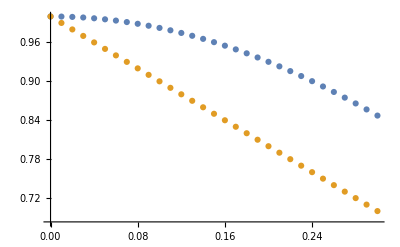

```mathematica
ListPlot[{Entfidpetz,Table[{i,1-i},{i,0,0.3,0.01}]}]
```

```mathematica
a=Table[Subscript[a1, i],{i,10}];
```

```mathematica
FindFit[Entfidpetz,1- Sum[a[[i]] x^i,{i,2,10}],a,x]
```

{a1_1→0.,a1_2→1.75,a1_3→0.292896,a1_4→-1.33221,a1_5→-1.26961,a1_6→1.46144,a1_7→1.42089,a1_8→-1.87544,a1_9→-0.371749,a1_10→0.987109}

```mathematica
γdep[75/10-0.1,0.1,0.005]
```

0.0108146

```mathematica
rhoI=ParallelTable[Sum[Bnm[t,i,j,k,l].base[[1]].ConjugateTranspose[Bnm[t,i,j,k,l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{t,0,50,0.1}];
```

```mathematica
rhox=ParallelTable[Sum[Bnm[t,i,j,k,l].base[[2]].ConjugateTranspose[Bnm[t,i,j,k,l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{t,0,50,0.1}];
```

```mathematica
rhoy=ParallelTable[Sum[Bnm[t,i,j,k,l].base[[3]].ConjugateTranspose[Bnm[t,i,j,k,l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{t,0,50,0.1}];
```

```mathematica
rhoz=ParallelTable[Sum[Bnm[t,i,j,k,l].base[[4]].ConjugateTranspose[Bnm[t,i,j,k,l]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{t,0,50,0.1}];
```

```mathematica
recI=ParallelTable[Sum[R[[i,j,k,l]].rhoI[[g]].ConjugateTranspose[R[[i,j,k,l]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{g,501}];
```

```mathematica
recx=ParallelTable[Sum[R[[i,j,k,l]].rhox[[g]].ConjugateTranspose[R[[i,j,k,l]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{g,501}];
```

```mathematica
recy=ParallelTable[Sum[R[[i,j,k,l]].rhoy[[g]].ConjugateTranspose[R[[i,j,k,l]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{g,501}];
```

```mathematica
recz=ParallelTable[Sum[R[[i,j,k,l]].rhoz[[g]].ConjugateTranspose[R[[i,j,k,l]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}],{g,501}];
```

```mathematica
rec=ParallelTable[{recI[[g]],recx[[g]],recy[[g]],recz[[g]]},{g,501}];
```

```mathematica
M=ParallelTable[Table[1/2 Tr[base[[i]].rec[[t]][[j]]],{i,1,4},{j,1,4}],{t,501}];
```

```mathematica
Evalmfour=ParallelTable[{t/10-0.1,Eigenvalues[M[[t]]][[j]]},{j,1,4},{t,121}](*markov_petz*);
```

```mathematica
r={{1},{x},{y},{z}};
```

```mathematica
fid=ParallelTable[Flatten[Transpose[r].Round[M[[t]],0.0001].r][[1]],{t,501}];
```

```mathematica
gam=Table[γdep[T,0.01,5],{T,0,20,0.1}];
```

```mathematica
wcffixed=ParallelTable[{t/10-0.1,0.5NMinimize[{fid[[t]],x^2+y^2+z^2==1},{x,y,z},Method->{"SimulatedAnnealing"}][[1]]},{t,501}];
```

```mathematica
wcfgm=ParallelTable[{gam[[t]],0.5NMinimize[{fid[[t]],x^2+y^2+z^2==1},{x,y,z},Method->{"SimulatedAnnealing"}][[1]]},{t,201}];
```

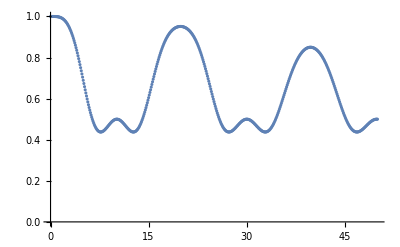

```mathematica
ListPlot[wcffixed]
```

```mathematica
wcfgm[[1]]
```

{0.,1.}

```mathematica
FindFit[wcfgm,1-a x-b x^2- c x^3- d x^4- e x^5- f x^6- g x^7,{a,b,c,d,e,f,g},x]
```

{a→0.00420916,b→1.57912,c→-0.790119,d→1.57057,e→-3.90574,f→2.84539,g→-0.803508}

```mathematica
Show[ListPlot[wcfgm,PlotStyle->{Red,Dotted,Thickness[0.00015]},PlotMarkers->":"],Plot[1-b x^2-c x^3-d x^4-e x^5-f x^6- g x^7/.{a->0.0042091584046083114,b->1.5791204886789172,c->-0.7901194347719458,d->1.5705668704263822,e->-3.9057445956740233,f->2.8453889970016046,g->-0.803508216133588},{x,0,0.9999643965175715}]]
```

-Graphics-

```mathematica
Show[ListPlot[wcffixed,PlotStyle->{Red,Thickness[0.0025]},PlotMarkers->"*"],Plot[1-b x^2-c x^3-d x^4-e x^5-f x^6/.{b->1.5906937847528124,c->-0.7050082612211022,d->0.7658013735106509,e->-1.8358528598050194,f->0.6832205091255474,x-> γdep[t,0.01,5]},{t,0.,50},PlotStyle->{Black,Thickness[0.0025]}]]
```

-Graphics-

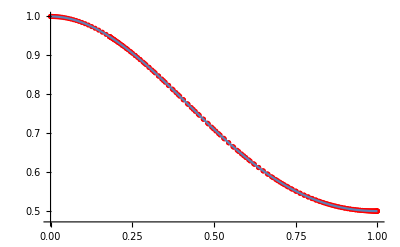

```mathematica
Show[ListPlot[wcfgm,PlotStyle->Red],Plot[1-b x^2-c x^3-d x^4-e x^5-f x^6/.{b->1.715272708071999,c->-0.3627338475460897,d->-2.3547828487018596,e->1.9306540161686787,f->-0.428333466304254},{x,0.,0.9999643965175715}]]
```

```mathematica
1- 1.715 γ^2+ 0.362 γ^3+2.35 γ^4-1.93 γ^5+ 0.428 γ^6
```

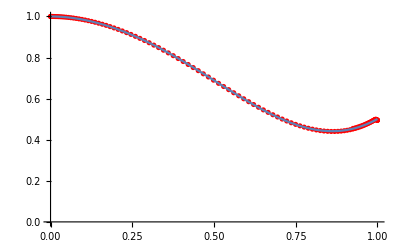

```mathematica
Show[ListPlot[wcfsixpetzfixed,PlotStyle->Red],Plot[1- b x^2- c x^3- d x^4- e x^5- f x^6/.{b->1.7044114825712513,c->-1.5040737403061575,d->2.813114506634679,e->-4.055917012753288,f->1.5413848360611409},{x,0.,0.9999643965175715}]]
```

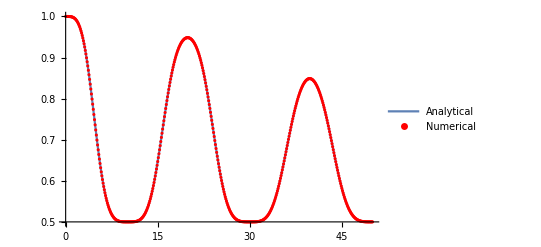
-Graphics-Worst case fidlityTime

```mathematica
Labeled[Show[Plot[1- b x^2- c x^3- d x^4- e x^5- f x^6/.{b->1.715272708071999,c->-0.3627338475460897,d->-2.3547828487018596,e->1.9306540161686787,f->-0.428333466304254,x->γdep[t,0.01,5]},{t,0,50},PlotRange->All,PlotLegends->Placed[{"Analytical"},{0.2,0.8}]],ListPlot[wcfsixpetzfixed,PlotStyle->Red,PlotLegends->Placed[{"Numerical"},{0.2,0.7}]]],{"Worst case fidlity","Time "},{Left, Bottom},RotateLabel->True]
```

```mathematica
Evalnmfour=ParallelTable[{t/10-0.1,Eigenvalues[M[[t]]][[j]]},{j,1,4},{t,501}](*nm_petz*);
```

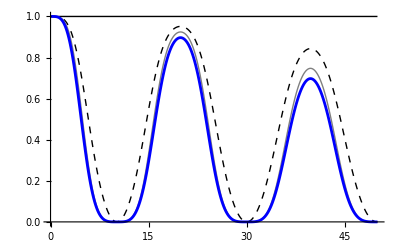
-Graphics-Eigenvalues of MTime →

```mathematica
plot2=Labeled[ListLinePlot[{Evalmfour[[1]],Evalmfour[[2]],Evalmfour[[3]],Evalmfour[[4]]},PlotStyle->{{Black,Thickness[0.0025]},{Black,Dashed,Thickness[0.0025]},{Gray,Thickness[0.0025]},{Blue,Thickness[0.005]}}],{"Eigenvalues of M","Time →"},{Left,Bottom},RotateLabel->True]
```

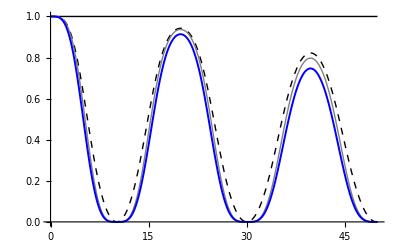
-Graphics-Eigenvalues of MTime →

```mathematica
plot1=Labeled[ListLinePlot[{Evalmfour[[1]],Evalmfour[[2]],Evalmfour[[3]],Evalmfour[[4]]},PlotStyle->{{Black,Thickness[0.0025]},{Black,Dashed,Thickness[0.0025]},{Gray,Thickness[0.0025]},{Blue,Thickness[0.0035]}}],{"Eigenvalues of M","Time →"},{Left,Bottom},RotateLabel->True]
```

```mathematica
,{Gray,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0025]},{Red,Thickness[0.0025]},{Black,Thickness[0.0025]}
```

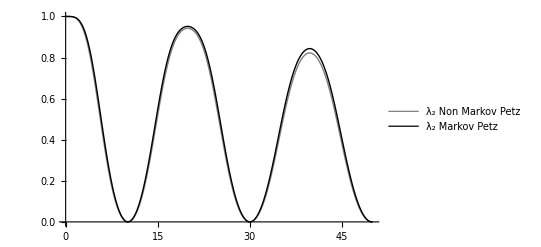
-Graphics-Eigenvalues of MTime →

```mathematica
Plot11=Labeled[ListLinePlot[{Evalmfour[[2]],Evalnmfour[[2]]},PlotStyle->{{Gray,Thickness[0.0025]},{Black,Thickness[0.0025]}},PlotLegends->Placed[{"λ_2 Non Markov Petz","λ_2 Markov Petz"},{0.7,0.89}]],{"Eigenvalues of M","Time →"},{Left,Bottom},RotateLabel->True]
```

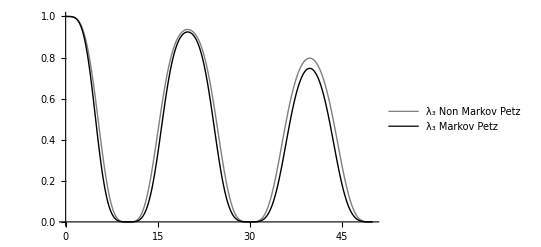
-Graphics-Eigenvalues of MTime →

```mathematica
Plot22=Labeled[ListLinePlot[{Evalmfour[[3]],Evalnmfour[[3]]},PlotStyle->{{Gray,Thickness[0.0025]},{Black,Thickness[0.0025]}},PlotLegends->Placed[{"λ_3 Non Markov Petz","λ_3 Markov Petz"},{0.7,0.89}]],{"Eigenvalues of M","Time →"},{Left,Bottom},RotateLabel->True]
```

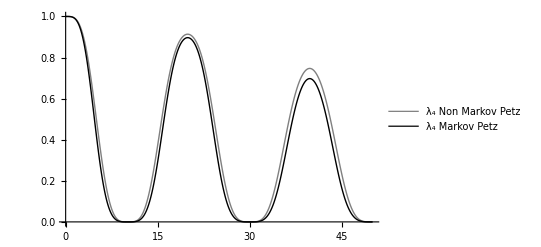
-Graphics-Eigenvalues of MTime →

```mathematica
Plot33=Labeled[ListLinePlot[{Evalmfour[[4]],Evalnmfour[[4]]},PlotStyle->{{Gray,Thickness[0.0025]},{Black,Thickness[0.0025]}},PlotLegends->Placed[{"λ_4 Non Markov Petz","λ_4 Markov Petz"},{0.7,0.89}]],{"Eigenvalues of M","Time →"},{Left,Bottom},RotateLabel->True]
```

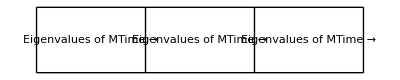

```mathematica
GraphicsRow[{Plot11,Plot22,Plot33},0.01,{Frame-> All}]
```

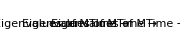

```mathematica
Show[%436,ImageSize->Small]
```

```mathematica
legends=LineLegend[{{Black,Thickness[0.0025]},{Black,Dashed,Thickness[0.0025]},{Gray,Thickness[0.0025]},Blue},{" λ_1"," λ_2 "," λ_3"," λ_4"},LegendFunction->(Framed[#,Background->Opacity[0.99,White]]&)]
```

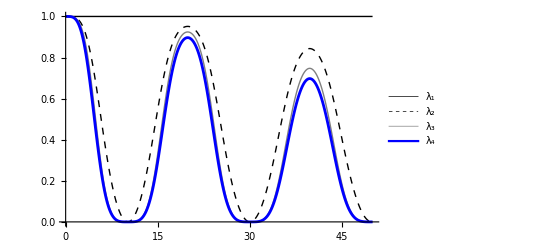
-Graphics-Eigenvalues of MTime →

```mathematica
Legended[plot2,legends]
```

```mathematica
funcevalfour=ParallelTable[Interpolation[Round[Evalnmfour[[j]],0.001]],{j,4}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
dλ1=funcevalfour[[2]]'
dλ2=funcevalfour[[3]]'
dλ3=funcevalfour[[4]]'
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
dλ2m=Round[Table[dλ3[x],{x,0,50,0.1}],0.00001]
```

{0.,0.,0.,0.,0.,0.,-0.00833,-0.00833,0.00167,-0.00333,-0.01167,-0.01,-0.01667,-0.02167,-0.02,-0.02333,-0.035,-0.04,-0.04,-0.04667,-0.06333,-0.06333,-0.075,-0.085,-0.08667,-0.09667,-0.11333,-0.11667,-0.13333,-0.14167,-0.15667,-0.16167,-0.16667,-0.18333,-0.19333,-0.20333,-0.20333,-0.215,-0.22167,-0.235,-0.24,-0.245,-0.25,-0.24167,-0.25167,-0.25,-0.25333,-0.25833,-0.25167,-0.24667,-0.24167,-0.24833,-0.235,-0.23167,-0.22667,-0.21833,-0.21667,-0.205,-0.195,-0.185,-0.17833,-0.17333,-0.15667,-0.14667,-0.13667,-0.13667,-0.125,-0.115,-0.10333,-0.09833,-0.09333,-0.07667,-0.07667,-0.07167,-0.06667,-0.055,-0.045,-0.03833,-0.04167,-0.03667,-0.02833,-0.02667,-0.02,-0.02,-0.02,-0.01667,-0.00833,-0.01,-0.00667,-0.00167,-0.00833,0.00167,-0.00333,-0.00833,0.00167,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00333,0.00333,-0.00167,0.00333,0.00833,0.00167,0.01,0.01,0.01333,0.01833,0.01167,0.01833,0.02333,0.03167,0.03,0.03333,0.03833,0.04333,0.05167,0.05333,0.06167,0.06667,0.07167,0.07333,0.085,0.09167,0.095,0.105,0.115,0.12167,0.12333,0.12667,0.13667,0.15,0.145,0.16333,0.16667,0.17167,0.17333,0.185,0.18833,0.195,0.2,0.19167,0.20167,0.2,0.19833,0.20333,0.20833,0.19833,0.2,0.2,0.2,0.19667,0.19,0.19,0.18667,0.17833,0.17667,0.17167,0.16667,0.155,0.14833,0.14667,0.13833,0.13667,0.125,0.115,0.10833,0.10667,0.09833,0.09667,0.085,0.07833,0.07667,0.06833,0.06667,0.055,0.04833,0.04667,0.03833,0.04,0.025,0.02,0.02833,0.015,0.00833,0.01167,0.00667,-0.00167,-0.00333,-0.01167,-0.01667,-0.02167,-0.02333,-0.03167,-0.03,-0.035,-0.045,-0.05167,-0.05,-0.05667,-0.06167,-0.06167,-0.075,-0.085,-0.09167,-0.08667,-0.09667,-0.11333,-0.11,-0.11333,-0.125,-0.135,-0.14167,-0.14333,-0.15167,-0.15667,-0.16167,-0.16333,-0.17167,-0.17333,-0.17833,-0.18333,-0.19167,-0.19,-0.19,-0.19833,-0.19833,-0.19167,-0.20167,-0.2,-0.19167,-0.19167,-0.19833,-0.18833,-0.18667,-0.18833,-0.18833,-0.175,-0.16833,-0.16667,-0.16,-0.16,-0.15333,-0.14,-0.145,-0.13167,-0.12667,-0.11833,-0.11667,-0.105,-0.09333,-0.08833,-0.09,-0.08667,-0.075,-0.06333,-0.05833,-0.06,-0.05667,-0.04833,-0.04333,-0.03833,-0.03667,-0.02833,-0.03,-0.02333,-0.01833,-0.02,-0.01667,-0.01167,-0.01333,-0.00833,-0.00667,-0.00167,-0.01167,-0.00333,0.00167,0.,-0.00333,-0.00833,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00333,0.00833,-0.00167,0.00333,0.00833,0.00167,0.01167,0.01,0.01,0.01,0.01333,0.01833,0.01167,0.02833,0.02833,0.02167,0.03167,0.03,0.03667,0.04167,0.04333,0.05167,0.05,0.055,0.065,0.06833,0.065,0.08,0.075,0.085,0.09167,0.09333,0.10167,0.1,0.10333,0.115,0.12167,0.12,0.12333,0.13167,0.13,0.13333,0.14167,0.14,0.14333,0.15167,0.14667,0.14167,0.15167,0.15333,0.15833,0.14833,0.15,0.15,0.14667,0.14167,0.14833,0.14167,0.145,0.13,0.13833,0.12833,0.13,0.12667,0.11833,0.11667,0.10833,0.10667,0.09833,0.09667,0.08833,0.09,0.08667,0.075,0.07167,0.06667,0.05833,0.05667,0.04833,0.04333,0.03833,0.03667,0.02833,0.02667,0.02167,0.01667,0.005,-0.00167,0.,-0.005,-0.015,-0.02167,-0.02,-0.02333,-0.03667,-0.04167,-0.04333,-0.05167,-0.05,-0.065,-0.07,-0.06167,-0.075,-0.08167,-0.08667,-0.09167,-0.09333,-0.10167,-0.10333,-0.11,-0.11,-0.11333,-0.12167,-0.12333,-0.12,-0.125,-0.14,-0.13167,-0.14167,-0.14,-0.14,-0.14333,-0.14833,-0.14167,-0.15,-0.15,-0.14667,-0.14167,-0.14833,-0.14833,-0.14833,-0.13833,-0.14,-0.13667,-0.13833,-0.13833,-0.125,-0.11833,-0.12,-0.12167,-0.11667,-0.10833,-0.10667,-0.09833,-0.09333,-0.08833,-0.08667,-0.07833,-0.08,-0.07333,-0.06833,-0.06667,-0.05833,-0.05667,-0.05,-0.05,-0.04667,-0.03833,-0.04,-0.03333,-0.02833,-0.03,-0.02667,-0.01833,-0.02,-0.02,-0.01667,-0.01167,-0.01833,-0.01,-0.01,-0.00667,-0.00167,-0.00833,-0.00833,-0.00833,0.00167,-0.00333,-0.00833,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

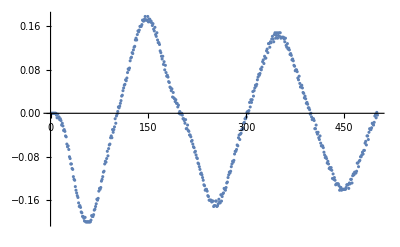

```mathematica
ListPlot[dλ1m]
```

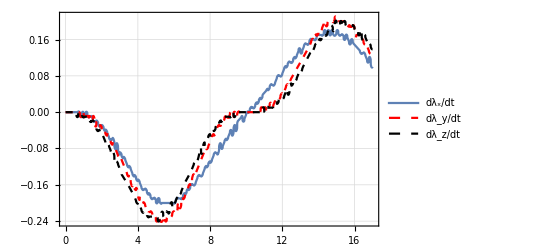
-Graphics-dλ/dt →Time →

```mathematica
Labeled[Plot[{dλ1[x],dλ2[x],dλ3[x]},{x,0.,17.},PlotStyle->{{Default},{Red,Dashed},{Black,Dashed}},PlotLegends->Placed[{"dλ_x/dt","dλ_y/dt","dλ_z/dt"},{0.75,0.25}],PlotTheme->"Detailed"],{"dλ/dt →","Time →"},{Left,Bottom},RotateLabel->True]
```

## Data:

Eigenvalues for the Markov petz

```mathematica
λ1=Round[{0.9999999999999885,0.9999999999999887,0.999999999999988,0.9999999999999882,0.9999999999999889,0.9999999999999903,0.9999999999999929,0.9999999999999944,0.9999999999999956,0.9999999999999959,0.9999999999999969,0.9999999999999969,0.9999999999999969,0.999999999999997,0.9999999999999974,0.9999999999999974,0.9999999999999969,0.9999999999999973,0.9999999999999967,0.9999999999999972,0.9999999999999978,0.9999999999999973,0.9999999999999969,0.9999999999999967,0.9999999999999969,0.9999999999999964,0.9999999999999966,0.9999999999999961,0.9999999999999954,0.9999999999999957,0.9999999999999952,0.9999999999999947,0.9999999999999947,0.9999999999999944,0.9999999999999943,0.9999999999999931,0.9999999999999929,0.9999999999999923,0.9999999999999919,0.9999999999999907,0.9999999999999907,0.9999999999999902,0.9999999999999902,0.9999999999999898,0.9999999999999892,0.9999999999999891,0.9999999999999876,0.9999999999999878,0.9999999999999869,0.9999999999999865,0.9999999999999862,0.9999999999999851,0.9999999999999853,0.9999999999999842,0.9999999999999836,0.9999999999999833,0.9999999999999833,0.9999999999999825,0.9999999999999822,0.999999999999982,0.9999999999999809,0.9999999999999805,0.9999999999999807,0.9999999999999791,0.99999999999998,0.9999999999999796,0.9999999999999787,0.9999999999999785,0.9999999999999785,0.9999999999999782,0.999999999999978,0.9999999999999769,0.9999999999999765,0.9999999999999776,0.9999999999999767,0.9999999999999765,0.999999999999976,0.9999999999999756,0.9999999999999756,0.9999999999999751,0.9999999999999747,0.9999999999999747,0.9999999999999738,0.9999999999999742,0.9999999999999736,0.9999999999999736,0.9999999999999734,0.9999999999999725,0.9999999999999725,0.9999999999999718,0.9999999999999718,0.9999999999999718,0.9999999999999714,0.9999999999999716,0.9999999999999711,0.9999999999999716,0.9999999999999702,0.9999999999999707,0.99999999999997,0.9999999999999707,0.9999999999999705,0.9999999999999705,0.9999999999999705,0.99999999999997,0.9999999999999698,0.9999999999999707,0.9999999999999709,0.9999999999999707,0.9999999999999705,0.9999999999999707,0.9999999999999711,0.9999999999999718,0.9999999999999716,0.9999999999999725,0.999999999999972,0.9999999999999727,0.9999999999999727,0.9999999999999729,0.9999999999999731,0.9999999999999736,0.999999999999974,0.999999999999974,0.9999999999999745,0.9999999999999738,0.9999999999999747,0.9999999999999751,0.9999999999999762,0.999999999999976,0.9999999999999765,0.9999999999999765,0.9999999999999765,0.9999999999999774,0.9999999999999776,0.9999999999999776,0.9999999999999785,0.9999999999999785,0.9999999999999787,0.9999999999999785,0.9999999999999791,0.9999999999999796,0.9999999999999796,0.99999999999998,0.99999999999998,0.9999999999999811,0.9999999999999809,0.9999999999999813,0.9999999999999825,0.9999999999999822,0.9999999999999822,0.9999999999999833,0.9999999999999836,0.9999999999999838,0.999999999999984,0.9999999999999845,0.9999999999999845,0.999999999999985,0.9999999999999858,0.9999999999999862,0.9999999999999862,0.9999999999999875,0.9999999999999876,0.999999999999988,0.9999999999999882,0.9999999999999888,0.9999999999999888,0.9999999999999897,0.9999999999999893,0.9999999999999901,0.9999999999999907,0.9999999999999909,0.9999999999999917,0.9999999999999911,0.9999999999999916,0.9999999999999926,0.9999999999999928,0.9999999999999926,0.9999999999999926,0.9999999999999936,0.9999999999999936,0.9999999999999941,0.999999999999994,0.9999999999999939,0.9999999999999944,0.9999999999999949,0.9999999999999944,0.9999999999999951,0.9999999999999948,0.9999999999999949,0.9999999999999953,0.9999999999999953,0.9999999999999951,0.9999999999999953,0.9999999999999957,0.9999999999999953,0.9999999999999951,0.9999999999999956,0.9999999999999951,0.9999999999999962,0.9999999999999961,0.9999999999999961,0.9999999999999958,0.9999999999999957,0.9999999999999956,0.9999999999999959,0.999999999999996,0.9999999999999958,0.9999999999999956,0.9999999999999957,0.9999999999999956,0.999999999999995,0.9999999999999953,0.9999999999999947,0.9999999999999951,0.9999999999999948,0.9999999999999943,0.9999999999999942,0.9999999999999951,0.9999999999999937,0.9999999999999946,0.9999999999999939,0.9999999999999936,0.9999999999999929,0.9999999999999929,0.9999999999999927,0.9999999999999927,0.999999999999992,0.9999999999999921,0.9999999999999913,0.9999999999999911,0.9999999999999905,0.9999999999999907,0.9999999999999898,0.9999999999999897,0.9999999999999889,0.9999999999999891,0.9999999999999885,0.9999999999999886,0.999999999999988,0.999999999999988,0.9999999999999871,0.999999999999987,0.9999999999999862,0.9999999999999851,0.9999999999999853,0.9999999999999856,0.9999999999999847,0.9999999999999842,0.999999999999984,0.9999999999999827,0.9999999999999836,0.9999999999999829,0.9999999999999822,0.9999999999999811,0.9999999999999818,0.9999999999999813,0.9999999999999811,0.9999999999999807,0.9999999999999798,0.9999999999999789,0.99999999999998,0.9999999999999791,0.9999999999999791,0.9999999999999787,0.9999999999999787,0.999999999999978,0.9999999999999774,0.9999999999999778,0.999999999999978,0.9999999999999774,0.9999999999999769,0.9999999999999765,0.9999999999999765,0.9999999999999758,0.9999999999999756,0.9999999999999756,0.9999999999999749,0.9999999999999747,0.9999999999999751,0.9999999999999747,0.9999999999999738,0.999999999999974,0.9999999999999738,0.9999999999999729,0.9999999999999736,0.9999999999999727,0.9999999999999729,0.9999999999999727,0.9999999999999722,0.9999999999999716,0.9999999999999718,0.999999999999972,0.9999999999999711,0.9999999999999711,0.9999999999999716,0.9999999999999709,0.9999999999999711,0.9999999999999705,0.9999999999999705,0.9999999999999705,0.9999999999999705,0.9999999999999702,0.9999999999999705,0.9999999999999705,0.9999999999999705,0.9999999999999707,0.9999999999999711,0.9999999999999716,0.9999999999999709,0.9999999999999711,0.9999999999999714,0.9999999999999711,0.9999999999999714,0.9999999999999718,0.9999999999999711,0.9999999999999729,0.9999999999999722,0.9999999999999727,0.9999999999999731,0.9999999999999738,0.9999999999999734,0.9999999999999736,0.9999999999999745,0.9999999999999745,0.9999999999999745,0.9999999999999751,0.9999999999999749,0.9999999999999751,0.9999999999999751,0.9999999999999754,0.999999999999976,0.9999999999999762,0.9999999999999762,0.9999999999999769,0.9999999999999769,0.9999999999999774,0.9999999999999771,0.999999999999978,0.9999999999999778,0.9999999999999785,0.9999999999999787,0.9999999999999785,0.9999999999999787,0.9999999999999796,0.99999999999998,0.99999999999998,0.9999999999999798,0.9999999999999802,0.9999999999999811,0.9999999999999809,0.9999999999999809,0.9999999999999813,0.9999999999999818,0.9999999999999822,0.9999999999999827,0.999999999999982,0.9999999999999831,0.9999999999999831,0.9999999999999831,0.9999999999999836,0.999999999999984,0.9999999999999851,0.9999999999999849,0.9999999999999851,0.9999999999999853,0.9999999999999857,0.9999999999999863,0.9999999999999865,0.9999999999999867,0.9999999999999866,0.9999999999999871,0.9999999999999871,0.999999999999988,0.9999999999999889,0.9999999999999889,0.9999999999999885,0.9999999999999885,0.9999999999999889,0.9999999999999891,0.9999999999999898,0.9999999999999899,0.9999999999999905,0.9999999999999898,0.9999999999999905,0.9999999999999899,0.9999999999999909,0.9999999999999909,0.9999999999999909,0.9999999999999913,0.9999999999999913,0.9999999999999913,0.9999999999999918,0.999999999999992,0.9999999999999911,0.9999999999999916,0.9999999999999911,0.9999999999999916,0.9999999999999918,0.9999999999999908,0.9999999999999922,0.9999999999999918,0.9999999999999913,0.9999999999999918,0.9999999999999916,0.9999999999999913,0.9999999999999916,0.9999999999999916,0.9999999999999912,0.9999999999999907,0.9999999999999911,0.9999999999999911,0.9999999999999907,0.9999999999999912,0.9999999999999905,0.9999999999999905,0.9999999999999898,0.99999999999999,0.9999999999999897,0.9999999999999899,0.9999999999999889,0.9999999999999889,0.999999999999988,0.9999999999999887,0.9999999999999882,0.9999999999999883,0.9999999999999878,0.9999999999999878,0.999999999999988,0.9999999999999871,0.9999999999999871,0.9999999999999865,0.9999999999999865,0.9999999999999857,0.9999999999999858,0.9999999999999851,0.9999999999999851,0.9999999999999845,0.999999999999984,0.9999999999999845,0.9999999999999838,0.9999999999999845,0.9999999999999833,0.9999999999999831,0.9999999999999825,0.9999999999999822,0.9999999999999816,0.9999999999999811,0.9999999999999813,0.9999999999999813,0.9999999999999805,0.9999999999999809,0.9999999999999796,0.9999999999999805,0.9999999999999798,0.99999999999998,0.9999999999999789,0.9999999999999789,0.9999999999999787,0.9999999999999791,0.9999999999999785,0.9999999999999782,0.9999999999999778,0.9999999999999782,0.9999999999999769,0.9999999999999771,0.9999999999999765,0.9999999999999762,0.999999999999976,0.9999999999999767,0.999999999999976,0.9999999999999749,0.9999999999999758,0.9999999999999756,0.9999999999999742,0.9999999999999747,0.9999999999999747,0.9999999999999738,0.9999999999999745,0.9999999999999736,0.9999999999999731,0.9999999999999734,0.9999999999999729,0.9999999999999736,0.9999999999999722,0.9999999999999725,0.9999999999999727,0.9999999999999718,0.9999999999999714,0.9999999999999711,0.9999999999999718,0.9999999999999711,0.9999999999999707,0.9999999999999707,0.9999999999999714,0.9999999999999707,0.9999999999999714,0.99999999999997,0.9999999999999707,0.9999999999999702,0.9999999999999705,0.9999999999999704,0.9999999999999705},0.00001];
```

```mathematica
λ2=Round[{0.999989746094949,0.9999884036927205,0.9999821433566266,0.9999642938890354,0.9999530595861403,0.9999313641060463,0.9998779215274429,0.9997769933223319,0.9996103391939131,0.999357384394991,0.9989954070063161,0.9984997435461602,0.9978440111375797,0.9970003443307693,0.9959396445656841,0.9946318401655811,0.9930461546760088,0.9911513813066154,0.9889161611953211,0.9863092631961247,0.9832998628931078,0.9798578185639721,0.9759539418563268,0.9715602609985378,0.966650274443581,0.9611991929382424,0.9551841681202722,0.9485845058716282,0.9413818627955823,0.9335604243378872,0.925107063236015,0.9160114771541732,0.9062663045438318,0.895867217958185,0.8848129942426861,0.8731055612207825,0.8607500206925339,0.847754647762194,0.8341308667073265,0.8198932037949686,0.8050592176380815,0.7896494078664289,0.7736871030586615,0.7571983290452405,0.7402116588436346,0.7227580456267372,0.7048706402515427,0.6865845949868443,0.6679368551751965,0.6489659406449477,0.629711718752194,0.6102151709796776,0.5905181550496322,0.5706631645203177,0.5506930878315045,0.5306509687426602,0.5105797700694589,0.4905221425698772,0.4705202007613165,0.4506153073655393,0.43084786797972646,0.4112571374605897,0.39188103938533947,0.3727559998196457,0.35391679647978674,0.33539642422535854,0.3172259776616054,0.29943455146812425,0.28204915890487253,0.26509466877859217,0.248593760984476,0.23256690057066096,0.2170323301084196,0.20200607999019923,0.18750199612232188,0.17353178433058059,0.1601050706563781,0.1472294765896869,0.13491070816403944,0.12315265772897813,0.11195751711779958,0.10132590084378242,0.09125697788702786,0.08174861057708968,0.0727974990341066,0.06439932960341918,0.056548925705773634,0.04924039952715745,0.042467302988915316,0.036222776469788685,0.030499693796453432,0.025290802077491195,0.020588855026840373,0.016386738505861184,0.012677587107356976,0.009454890709226744,0.006712590038850739,0.0044451604106921965,0.0026476829277362265,0.0013159025710461933,0.0004462727396052705,0.00003598594340906199,0.00008299049515245126,0.0005859931884789268,0.0015444480922895572,0.0029585317297417747,0.00482910504602717,0.0071576626995526246,0.009946270335597949,0.01319749061874359,0.016914298909337513,0.021099989569007646,0.02575807396988779,0.03089217136100981,0.036505893812580605,0.04260272651403395,0.049185904744398205,0.05625828886331466,0.06382223868778773,0.07187948862335247,0.08043102490886182,0.08947696631166575,0.09901644957487998,0.1090475208710917,0.11956703445774464,0.1305705596591859,0.1420522972196611,0.15400500598118388,0.1664199407411212,0.17928680203741393,0.19259369849569133,0.2063271222531735,0.22047193785033264,0.23501138485398423,0.24992709434597063,0.26519911928110085,0.2808059785877412,0.2967247147555804,0.3129309645288525,0.32939904220079763,0.3461020348875136,0.3630119090476774,0.38009962740984454,0.3973352753721984,0.414688195851471,0.43212713147916526,0.4496203729748136,0.4671359124683924,0.48464160049773647,0.5021053053721346,0.5194950735706458,0.536779289833113,0.5539268356034889,0.5709072444988751,0.5876908535033887,0.6042489486234293,0.6205539037896743,0.6365793118507262,0.65230010657325,0.6676926746429003,0.6827349567487376,0.6974065369302154,0.7116887194693815,0.725564592720706,0.7390190793858601,0.7520389728598753,0.7646129593972466,0.7767316259706337,0.7883874538197473,0.7995747978126638,0.8102898518650337,0.8205306007834289,0.8302967590162356,0.8395896969080929,0.8484123551608767,0.8567691483046771,0.8646658580753356,0.872109517679936,0.8791082880076381,0.8856713269096058,0.8918086527280509,0.897531003300096,0.9028496916968698,0.907776459981781,0.91232333228401,0.9165024684839437,0.9203260197965454,0.9238059875166196,0.926954086156915,0.9297816121662383,0.9322993193607743,0.9345173021380206,0.9364448874698719,0.9380905365900016,0.9394617572016188,0.9405650269357191,0.9414057286879413,0.9419880983550828,0.9423151853811103,0.9423888264081697,0.9422096322116567,0.9417769879808928,0.9410890668893879,0.9401428567821252,0.9389341996927548,0.9374578437920631,0.9357075072615317,0.9336759534831698,0.9313550768399372,0.928735998330826,0.9258091701217791,0.9225644880787855,0.9189914112633315,0.9150790873134168,0.9108164825860494,0.9061925158998525,0.9011961946894106,0.895816752366505,0.8900437856774092,0.8838673908500477,0.8772782973399054,0.8702679980088956,0.8628288746067612,0.8549543174695317,0.8466388384037044,0.8378781757876208,0.8286693909923342,0.8190109553025091,0.8089028266027684,0.7983465151856495,0.7873451381331457,0.7759034618237637,0.764027932220281,0.7517266926989792,0.7390095892881305,0.7258881632910001,0.7123756313755956,0.6984868533190164,0.6842382876974776,0.6696479359131577,0.6547352750450003,0.6395211801016716,0.6240278363403852,0.608278642394364,0.5922981050238477,0.5761117263700591,0.5597458846479879,0.5432277092617301,0.526584951365151,0.5098458509204595,0.4930390013278057,0.47619321270997483,0.45933737493782856,0.4425003214741835,0.4257106950966289,0.4089968165335165,0.3923865570122679,0.3759072156757544,0.3595854027710679,0.3434469294562443,0.32751670500480845,0.31181864211614674,0.296375570962339,0.2812091625198575,0.26633986164833223,0.2517868302891382,0.23756790106464526,0.22369954146557755,0.21019682871968806,0.19707343534091257,0.18434162526502113,0.1720122603863945,0.16009481722178356,0.14859741334139642,0.1375268431262785,0.1268886223343076,0.11668704088586902,0.10692522321507185,0.09760519547362635,0.0887279588228379,0.08029356800484108,0.07230121434768627,0.06474931233031112,0.05763558881311173,0.050957174027765895,0.044710693416295036,0.03889235941395239,0.033498062283373764,0.02852345912825105,0.023964060243404722,0.0198153119941808,0.01607267546118276,0.012731700136068738,0.0097880920099341,0.007237775457152925,0.005076948383843639,0.003302130180706843,0.00191020209420634,0.0008984397071937681,0.00026453729941073234,6.6239390851577485*^-6,0.0001232712383344801,0.0006134927865341991,0.0014767353564829368,0.002712862057339454,0.004322127685234583,0.006305146596464504,0.008662853498616705,0.011396457621219703,0.014507390789000344,0.017997249977014136,0.021867734977335563,0.026120581851211227,0.03075749287824868,0.0357800637450143,0.04118970873912195,0.046987584731344706,0.0531745147373417,0.05975091185227113,0.06671670434584534,0.07407126269239225,0.08181332929040755,0.08994095159906855,0.09845141938562746,0.10734120673774705,0.1166059194491642,0.1262402483359838,0.1362379289849265,0.14659170837450147,0.15729331874594443,0.1683334590334699,0.17970178409349935,0.1913869019008167,0.203376378806575,0.21565675287957745,0.22821355527880208,0.24103133953249736,0.25409371852797497,0.26738340894708956,0.28088228281596334,0.2945714257743689,0.3084312016108549,0.322441322554798,0.33658092476640467,0.3508286484208697,0.36516272174370196,0.3795610483209637,0.39400129698123243,0.4084609935255157,0.42291761356743174,0.4373486757387508,0.45173183451484566,0.46604497192084454,0.48026628739202715,0.4943743850812897,0.5083483579319915,0.5221678678659806,0.5358132214737811,0.5492654406363489,0.5625063275551732,0.5755185237193241,0.5882855623937377,0.6007919142722544,0.6130230260009364,0.6249653513415483,0.6366063748111355,0.6479346277007612,0.658939696444147,0.6696122233744343,0.6799438999740888,0.6899274527884315,0.6995566222367977,0.708826134616419,0.7177316676521548,0.7262698099997313,0.7344380151607006,0.7422345503134025,0.7496584406055402,0.7567094094900678,0.7633878157167429,0.7696945876166468,0.7756311553359825,0.7811993816884568,0.7864014923023884,0.7912400057393448,0.7957176642556925,0.7998373658668751,0.8036020983568462,0.807014875851867,0.8100786785492471,0.8127963961576987,0.8151707755672517,0.8172043732233971,0.8188995126328037,0.820258247376952,0.8212823299558977,0.8219731867275557,0.8223318991489682,0.8223591914654845,0.8220554249322065,0.8214205985900145,0.8204543565565197,0.8191560017309607,0.8175245157519502,0.8155585849885407,0.8132566322889492,0.8106168541578358,0.8076372629828319,0.804315733884428,0.8006500557208255,0.7966379857412246,0.7922773073476506,0.7875658903970357,0.7825017534521652,0.7770831273723675,0.7713085196227119,0.7651767786739624,0.7586871578647322,0.7518393781021186,0.7446336887875381,0.7370709263703902,0.7291525699534053,0.7208807933998308,0.71225851342378,0.7032894331807501,0.6939780809152065,0.684329843265874,0.6743509928764719,0.6640487100098047,0.6534310979157437,0.6425071917583416,0.6312869609635978,0.619781304906651,0.6080020419150516,0.5959618916225933,0.5836744507655467,0.5711541625694968,0.5584162799298387,0.5454768226418775,0.5323525289869518,0.5190608020285501,0.50561965101676,0.4920476283400079,0.47836376249977897,0.4645874876163525,0.45073857000144507,0.43683703235671867,0.42290307617516576,0.4089570029354354,0.3950191346869665,0.38110973462639575,0.36724892826313593,0.35345662576418996,0.33975244605548105,0.32615564323918267,0.3126850358640346,0.29935893955861337,0.28619510350622024,0.2732106512048535,0.26042202591685165,0.247844941170692,0.23549433663245195,0.22338433961699172,0.21152823245947822,0.19993842591682268,0.18862643871645074,0.17760288331703836,0.16687745789283637,0.1564589445005368,0.14635521333565304,0.13657323293464918,0.12711908612994155,0.11799799151783008,0.10921433015483119,0.10077167715613324,0.09267283783131956,0.08491988795746204,0.0775142177583853,0.07045657913170869,0.06374713564227422,0.05738551478202643,0.05137086198243204,0.04570189585616852,0.04037696414019888,0.03539409981240856,0.03075107685873729,0.026445465177083266,0.022474684118088426,0.018836054181079698,0.01552684640573663,0.012544329026258662,0.009885810984669058,0.007548681933093081,0.005530448391107303,0.0038287657631861857,0.0024414659625489037,0.0013665804309119167,0.0006023583884096995,0.00014728019382871432,6.574190679810779*^-8,0.00015967787134472076},0.00001];
```

```mathematica
Round[7.*10^-6,0.00001]//N
```

0.00001

```mathematica
λ3=Round[{0.9999420543874102,0.9999446186990408,0.99995080190869,0.9999560988376497,0.9999242685092914,0.9998920139274353,0.9998254172858303,0.9997084415096766,0.9995223648330827,0.9992458910319321,0.9988552759040421,0.9983244702725032,0.9976252797510985,0.9967275414465345,0.9955993176804121,0.994207106694545,0.9925160701572303,0.9904902771168683,0.9880929638550828,0.9852868088769365,0.9820342220443102,0.9782976466138767,0.9740398726875927,0.9692243603259718,0.963815570317503,0.9577793003466089,0.9510830240627505,0.9436962303299623,0.9355907597344044,0.9267411352524539,0.9171248838381572,0.9067228455808055,0.8955194670149501,0.8835030751395716,0.870666128723178,0.8570054435392962,0.8425223882935254,0.8272230481695537,0.8111183531370654,0.7942241684282656,0.7765613448999258,0.7581557273517735,0.7390381192662836,0.7192442028653253,0.6988144138407946,0.6777937706039217,0.6562316584053274,0.6341815691986504,0.6117007986478779,0.5888501022052207,0.5656933127052479,0.542296922424696,0.518729633038584,0.4950618773549231,0.47136531712554675,0.4477123216029243,0.42417543183634454,0.4008268159700689,0.3777377210163382,0.35497792672338857,0.3326152072397949,0.31071480628918646,0.28933893151226303,0.26854627350571486,0.2483915548905738,0.22892511447722372,0.2101925312632492,0.1922342926068179,0.17508551046673754,0.1587756890957146,0.14332854702163306,0.12876189555939044,0.11508757547019441,0.10231145273391413,0.0904334737312076,0.0794477794541305,0.06934287768531461,0.060101871415276294,0.05170274111354056,0.04411867784046024,0.037318463591003666,0.031266894707080314,0.025925243688384784,0.021251754279840402,0.01720216432241547,0.013730250528446095,0.010788389086887304,0.00832812582143979,0.006300749517637006,0.004657862005099565,0.0033519386286237143,0.002336872865930074,0.001568499049095334,0.0010050874182930573,0.0006078060769103646,0.0003411448219203443,0.00017329628729238438,0.00007649035517693902,0.000027278352904100913,6.764156214172435*^-6,7.79952847494066*^-7,5.077551342628099*^-9,2.7001353299450927*^-8,1.344236104140283*^-6,9.311591287666268*^-6,0.00003402888550105773,0.00009017486160312589,0.00019678867439897274,0.0003770019053854341,0.0006577246035433678,0.0010692893480558463,0.0016450577724617973,0.0024209943751842948,0.003435212764468458,0.004727499743255966,0.0063388228290246216,0.00831082692366425,0.010685325898489632,0.013503794839873342,0.016806868612975572,0.020633852246785368,0.025022248426120407,0.030007307099100728,0.0356216018763464,0.0418946375158475,0.048852492360755125,0.05651749913237667,0.06490796698392165,0.0740379471988624,0.08391704437810701,0.0945502744096491,0.10593796996002858,0.11807573367579756,0.1309544387420403,0.1445602759203523,0.15887484568669055,0.17387529361589188,0.18953448671959727,0.20582122804249045,0.22270050646214762,0.24013377832377555,0.2580792772753909,0.27649234845345355,0.29532580300498396,0.3145302888201647,0.3340546732892998,0.3538464338888662,0.3738520524417376,0.39401740898443105,0.4142881713066704,0.434610176402553,0.45492980028446656,0.4751943128566339,0.4953522148204225,0.5153535538837466,0.5351502178672899,0.5546962026360283,0.5739478531307283,0.5928640761260254,0.6114065236944745,0.6295397467052796,0.647231318027813,0.6644519254396111,0.6811754345526828,0.6973789223672721,0.7130426823360502,0.7281502020714686,0.7426881150528828,0.7566461278865081,0.7700169248393567,0.7827960515074109,0.7949817795884657,0.8065749548115387,0.8175788301283875,0.827998886299559,0.8378426420090245,0.8471194556196643,0.8558403206385599,0.8640176568986422,0.8716650993839528,0.8787972865322287,0.8854296497432153,0.8915782057065975,0.8972593530423002,0.9024896746204852,0.9072857468012638,0.9116639567070282,0.9156403285153579,0.9192303596393884,0.9224488675468033,0.9253098478594609,0.9278263442739729,0.9300103307500288,0.9318726063282193,0.9334227028626767,0.9346688058858772,0.9356176887629667,0.9362746602404369,0.9366435254479761,0.9367265603719314,0.9365244997828733,0.936036538567052,0.9352603463807755,0.9341920955166434,0.9328265018397931,0.9311568786196689,0.9291752030470971,0.9268721951866444,0.9242374090694278,0.9212593355810288,0.917925516742436,0.9142226709186795,0.9101368284199881,0.905653476884036,0.9007577157456267,0.8954344190125963,0.8896684054747442,0.883444615377365,0.8767482924937354,0.8695651704333203,0.8618816619261245,0.8536850497303824,0.8449636777225682,0.8357071406475184,0.8259064709342601,0.8155543209219932,0.80464513879245,0.7931753364714714,0.7811434477457564,0.7685502748419114,0.7553990217355319,0.7416954124990811,0.7274477930597265,0.7126672148224674,0.6973674987201386,0.6815652783799997,0.6652800212461657,0.6485340266673287,0.6313524001487695,0.6137630031751725,0.5957963782343095,0.5774856489090501,0.5588663951540771,0.5399765041312222,0.5208559972407076,0.50154683425157,0.48209269569988017,0.4625387449846826,0.4429313718454239,0.42331791914754013,0.40374639513150373,0.38426517349153855,0.36492268384044385,0.3457670952833201,0.32684599596293845,0.30820607155048757,0.28989278573533434,0.2719500658146321,0.25441999649652586,0.2373425250086607,0.22075518054594104,0.2046928109981643,0.18918733976962362,0.17426754533987102,0.15995886601901146,0.14628323212389824,0.1332589275456051,0.12090048239634334,0.10921859811838593,0.09822010611209767,0.08790796059836427,0.07828126607651296,0.06933533937637368,0.06106180593659035,0.0534487295751206,0.04648077465637445,0.0401393992070086,0.03440307719336073,0.029247547851934595,0.024646089664300784,0.020569816292875548,0.01698799154779857,0.01386836024054973,0.011177491599797772,0.00888113178148491,0.006944561900200576,0.005332957943804468,0.004011748908922828,0.0029469695116941946,0.0021056038858564105,0.0014559167782730626,0.0009677688891422435,0.0006129131787804302,0.0003652691729155163,0.00020117254133069203,0.00009959749753256853,0.000042349866577984044,0.000014228990671326677,3.1569837524640105*^-6,2.742029342679327*^-7,1.7205151743724142*^-10,5.956637480612124*^-8,1.473243297290814*^-6,8.514677097171759*^-6,0.0000286325223551087,0.00007234038602125874,0.00015307522840978365,0.00028702613470000393,0.0004929354972612414,0.0007918749220248669,0.001206998416282882,0.001763275628165222,0.0024872080875151183,0.003406531542259917,0.0045499075924253845,0.005946607894894581,0.0076261942455587055,0.009618197841798298,0.011951800987884318,0.01465552442994176,0.017756923397040547,0.021282295282647426,0.02525640172828081,0.02970220767135836,0.03464063969471527,0.04009036576922353,0.04606759821664765,0.05258592144078779,0.059656145684649366,0.06728618777347468,0.07548097950163282,0.0842424040191528,0.09356926027471951,0.1034572552795235,0.11389902367384477,0.12488417380857485,0.13639935929993105,0.14842837477989987,0.16095227434970785,0.17394951105079143,0.1873960954989334,0.20126577168366347,0.21553020781769847,0.23015920003050314,0.2451208866363733,0.2603819706705305,0.27590794837610394,0.2916633413399031,0.30761193001430126,0.323716986425187,0.33994150395014255,0.3562484221549528,0.3726008447984067,0.3889622492528045,0.4052966857386089,0.4215689649338157,0.4377448326895918,0.4537911307611994,0.469675942644729,0.4853687237935762,0.5008404156716262,0.5160635432806128,0.5310122959752709,0.5456625915497643,0.5599921237408734,0.5739803934461188,0.5876087240970946,0.6008602617588163,0.6137199606439171,0.6261745548355094,0.6382125171040702,0.6498240057814629,0.6610008007193726,0.6717362294099488,0.6820250843838099,0.6918635330252143,0.7012490209566843,0.7101801701465977,0.7186566728838545,0.726679182744775,0.7342492036497605,0.7413689780719633,0.7480413754183142,0.7542697815557105,0.7600579904029691,0.765410098453312,0.7703304030334266,0.7748233050445332,0.7788932168689754,0.782544476063437,0.7857812653974289,0.7886075397337647,0.79102696018664,0.7930428359330116,0.7946580739943704,0.7958751372488733,0.7966960108781102,0.7971221773985592,0.7971546003748632,0.7967937168603052,0.7960394385591132,0.7948911616552248,0.7933477852026752,0.7914077379236939,0.7890690132115511,0.7863292120861959,0.7831855938014907,0.7796351337533769,0.7756745882885588,0.7713005659633202,0.7665096047520018,0.7612982546546874,0.7556631651040321,0.7496011765223138,0.7431094153320581,0.7361853916775993,0.7288270990711512,0.7210331151361006,0.7128027025829229,0.7041359095200992,0.6950336681744128,0.6854978910727983,0.6755315637221704,0.6651388328152249,0.6543250889896177,0.6430970431759159,0.6314627955868125,0.6194318964267144,0.6070153974374327,0.5942258934424854,0.5810775531096282,0.5675861382187226,0.5537690107996269,0.539645127592394,0.5252350213789982,0.5105607688416761,0.495645944716893,0.48051556213509083,0.4651959991636895,0.4497149117031304,0.4341011330217178,0.41838456035338767,0.40259602912157766,0.38676717549080564,0.37093028808349937,0.3551181498316002,0.33936387105874605,0.32370071500770436,0.30816191713772734,0.2927804996158979,0.27758908251393294,0.2626196932959858,0.2479035762423153,0.23347100349739172,0.2193510894579503,0.20557161022602977,0.1921588298435592,0.17913733499817644,0.16652987984464343,0.15435724252242303,0.1426380948681051,0.1313888867219179,0.12062374611128866,0.1103543964623558,0.10059009184361856,0.09133757108596538,0.08260103145175193,0.07438212234407261,0.06667995935788172,0.05949115877907494,0.0528098924382612,0.04662796262485743,0.040934896566597136,0.0357180597818114,0.030962787419185296,0.026652532514297576,0.022769029916315114,0.019292474473737237,0.016201711917083254,0.01347444074061097,0.011087423266229943,0.009016703972148639,0.007237833087696021,0.005726093395221479,0.004456728140743617,0.0034051679376352925,0.002547254552355235,0.0018594594880820647,0.001319095330823554,0.0009045178926531353,0.000595317277411796,0.0003724961045095238,0.0002186332551325166,0.0001180316507760364,0.00005684873493389981,0.000023208503177249848,7.294112778475898*^-6,1.4202983911650331*^-6,8.502288789635457*^-8,1.6948012423704486*^-14,9.993575122794108*^-8},0.00001];
```

```mathematica
λ4=Round[{0.9999318016451638,0.9999332101201819,0.9999359263885556,0.9999354391425441,0.9999238264505812,0.999845479334386,0.9997099247743936,0.9994939761176471,0.9991708333306555,0.9987103644701442,0.9980794204313888,0.9972421799957377,0.9961605219353363,0.9947944206997087,0.9931023620076773,0.9910417745007545,0.9885694734819811,0.9856421126682136,0.9822166398247779,0.9782507521295747,0.9737033471291291,0.9685349652014756,0.9627082195294353,0.9561882097118929,0.9489429152987958,0.9409435657262024,0.9321649833489952,0.9225858965186596,0.9121892199295136,0.9009622997563212,0.8888971214265997,0.8759904782091266,0.8622440991531422,0.847664735277236,0.8322642032796752,0.8160593864195552,0.7990721925973083,0.7813294700403752,0.7628628813718809,0.7437087372037195,0.7239077907473208,0.7035049952724611,0.6825492265639433,0.6610929728249781,0.6391919947521315,0.616904958757472,0.594293046536867,0.5714195443774908,0.5483494157608859,0.5251488609491107,0.5018848673395762,0.4786247544384843,0.4554357173328539,0.4323843725369543,0.4095363100507198,0.38695565539592025,0.36470464529137103,0.3428432204922827,0.3214286391524769,0.30051511387313856,0.2801534753800114,0.2603908655245316,0.24127046203564034,0.22283123716045708,0.20510775202625137,0.18812998823602803,0.17192321787846757,0.1565079127928879,0.1418996935844254,0.1281093185367856,0.11514271222282521,0.10300103326992532,0.09168078040061299,0.08117393554212138,0.07146814248435462,0.06254691926676634,0.05438990219347936,0.04697311911497523,0.04026928937602155,0.034248147615159465,0.028876788412782205,0.0241200286240962,0.01994078410131392,0.01630045740726319,0.013159333050928788,0.010476976734697762,0.008212635093430353,0.006325632426799859,0.004775760978251768,0.0035236613957699715,0.00253119012047745,0.0017617705877812414,0.0011807252908800278,0.0007555859463551978,0.00045637921442034875,0.0002558856601720023,0.00012986989466162797,0.000057280103436064436,0.000020415452882183808,5.060158669162189*^-6,5.833031304126415*^-7,3.796832653512677*^-9,2.019107330077567*^-8,1.0053598523721712*^-6,6.966379220502548*^-6,0.00002547023609035982,0.00006753629495905573,0.00014749673695622852,0.0002828264587488127,0.0004939441767722696,0.0008039867228446399,0.0012385587384472273,0.0018254601750060519,0.0025943941847609234,0.0035766581398623412,0.004804820645009063,0.006312387510289154,0.008133459725208708,0.010302386521729798,0.01285341663328155,0.015820350848196035,0.01923619892013566,0.02313284383535416,0.027540716347824366,0.03248848257936929,0.03800274734415013,0.044107775696614365,0.050825235020874354,0.05817395977927575,0.06616974082052657,0.07482514091529202,0.08414933794179832,0.0941479968880169,0.1048231715728049,0.11617323671837054,0.1281928507330749,0.1408729492893604,0.15420076950894487,0.1681599042987993,0.18273038611919015,0.19788879921151037,0.21360841907098282,0.2298593777196269,0.2466088531201711,0.2638212808735947,0.2814585861633992,0.2994804337499935,0.31784449367996237,0.3365067202586416,0.3554216417411031,0.37454265812711396,0.3938223444002371,0.41321275653024214,0.4326657375613767,0.4521332211365572,0.4715675298587778,0.49092166596530495,0.5101495918866674,0.5292064983800815,0.5480490580643891,0.5666356623396014,0.5849266398470104,0.602884454813926,0.6204738838286108,0.6376621698038529,0.6544191521099743,0.6707173720876716,0.6865321533858558,0.7018416568073803,0.7166269095840556,0.7308718092393776,0.7445631024309305,0.7576903393921643,0.7702458048133265,0.782224426211656,0.7936236610397207,0.80444336396629,0.8146856359346633,0.8243546567576132,0.8334565031446106,0.8419989541747271,0.8499912863266009,0.8574440602542752,0.8643689015541264,0.8707782778029507,0.8766852741605597,0.8821033698218668,0.8870462175736558,0.891527428660499,0.8955603650931272,0.8991579414418405,0.9023324380481781,0.9050953274611988,0.9074571157616349,0.909427200279279,0.9110137450378317,0.9122235750786949,0.9130620906226274,0.9135332018276349,0.9136392846948129,0.9133811584630793,0.9127580846207938,0.9117677874491198,0.9104064958006706,0.9086690056093878,0.9065487624256799,0.9040379630764007,0.9011276753640941,0.897807974545686,0.8940680951690725,0.8898965966982625,0.8852815412251998,0.8802106814502599,0.874671657014729,0.868652197188124,0.8621403278517508,0.855124580677818,0.8475942023811602,0.8395393619182029,0.8309513535252699,0.8218227935254112,0.8121478088892151,0.801922215610018,0.7911436850467715,0.7798118964976507,0.7679286743932912,0.7554981086390429,0.7425266567896145,0.7290232269053907,0.7149992401160915,0.7004686721026314,0.6854480729003111,0.6699565646240933,0.65401581691788,0.6376500001325414,0.6208857164401945,0.6037519092929196,0.5862797518311398,0.568502515038241,0.550455416622222,0.5321754517804269,0.5137012071682077,0.49507265954532864,0.4763309607135576,0.4575182104841159,0.43867721952331606,0.419851264017872,0.40108383417724475,0.3824183786483538,0.3638980469575196,0.34556543211541785,0.3274623155227791,0.30962941629785257,0.29210614711119326,0.2749303785597045,0.25813821404048665,0.24176377699656126,0.2258390123019156,0.2103935034333173,0.19545430694230398,0.1810458055936523,0.16718958137797993,0.15390430943728273,0.1412056737646386,0.1291063053546807,0.11761574329134267,0.10674041906545136,0.09648366421881474,0.08684574121507427,0.07782389724263468,0.06941244046303137,0.06160283803084303,0.054383835030353406,0.04774159330107356,0.041659848960518046,0.03612008727961134,0.031101733425073066,0.02658235745530809,0.022537891842689894,0.01894285969667682,0.015770611779644783,0.01299357034137685,0.01058347774924204,0.008511647859627353,0.006749218062297371,0.005267399933118573,0.004037726451847735,0.0030322937802027545,0.0022239956507637214,0.0015867484888465512,0.0010957054766359382,0.000727457870724724,0.0004602219998309726,0.0002740104977693436,0.0001507864665702978,0.00007459941469461118,0.00003170197423038945,0.000010646567365173942,2.3613648178963613*^-6,2.0505577514327211*^-7,1.286534474127851*^-10,4.4543139182980814*^-8,1.1018548734819466*^-6,6.370033296922589*^-6,0.000021429389018790286,0.000054170198138765945,0.00011470077578695678,0.0002152369083876833,0.00036997370249491955,0.000594941046282129,0.0009078440067809462,0.0013278896007440297,0.0018756014786615379,0.0025726241492159607,0.0034415184446682477,0.004505549985815519,0.005788472447868858,0.0073143074556232535,0.009107122947534574,0.011190811843810412,0.013588872833537552,0.01632419506052659,0.019418848437371225,0.022893881252794485,0.026769126659340014,0.03106301953768506,0.03579242513120248,0.04097248073088174,0.0466164515674214,0.05273560193539474,0.059339082435111795,0.06643383407239736,0.07402450980637815,0.08211341398178168,0.09070045992668557,0.0997831458403935,0.109356548940605,0.11941333768561196,0.1299438017372317,0.14093589918485175,0.15237532041155985,0.16424556785099337,0.17652805075944777,0.189202194012797,0.2022455598329726,0.21563398125485161,0.2293417060621164,0.24334154985069192,0.25760505682105667,0.2721026668565807,0.28680388741424817,0.30167746873676843,0.316691580891293,0.3318139911494466,0.3470122402460737,0.36225381608954393,0.37750632354421343,0.39273764896517827,0.407916118235999,0.42301064714097397,0.4379908829939021,0.45282733654408563,0.46749150328675304,0.48195597341790475,0.4961945297917974,0.5101822333617048,0.5238954957100278,0.5373121384011779,0.5504114390185633,0.5631741638744561,0.5755825875072251,0.5876204992032315,0.5992731968995886,0.610527468937781,0.6213715642459194,0.6317951516282022,0.6417892689330278,0.6513462629555006,0.6604597210049282,0.669124395132828,0.6773361200713984,0.6850917259759178,0.6923889470968629,0.6992263275284478,0.7056031251896631,0.7115192151918676,0.716974993733483,0.7219712836378179,0.7265092426146258,0.7305902752802698,0.7342159499157387,0.7373879208769207,0.7401078574981326,0.7423773802487276,0.7441980048144915,0.7455710946813736,0.7464978226998369,0.7469791420047622,0.7470157665593916,0.746608161483308,0.7457565432150011,0.744460889450187,0.7427209586888007,0.7405363191175507,0.7379063864520133,0.7348304702635833,0.7313078282229782,0.7273377276043891,0.7229195133135633,0.7180526816298729,0.7127369587874046,0.7069723834639657,0.7007593922000798,0.6940989067330499,0.6869924222042334,0.6794420951811482,0.6714508304299368,0.6630223653782069,0.6541613512231875,0.6448734296654112,0.6351653042834441,0.6250448056102562,0.6145209490261327,0.6036039846461672,0.5923054384516486,0.5806381439934374,0.5686162640810036,0.5562553019622601,0.5435721015959856,0.5305848367194301,0.5173129885177776,0.5037773118085704,0.48999978976185216,0.4760035772848841,0.46181293330761053,0.4474531423107746,0.4329504255416462,0.4183318424618094,0.4036251830664599,0.3888588518043102,0.3740617439106052,0.359263115042319,0.3444924451733834,0.32977929776844095,0.31515317530530984,0.300643372258797,0.28627882669126037,0.27208797161800186,0.2580985873281446,0.2443376558438201,0.23083121869229245,0.2176042391472195,0.20468047006656642,0.19208232841621165,0.17983077752017235,0.16794521802113058,0.15644338846905947,0.14534127638173583,0.13465304053954003,0.12439094518876848,0.11456530673357238,0.10518445339736919,0.09625469823100287,0.08778032573799092,0.07976359227776404,0.07220474029684773,0.06510202632643011,0.058451762573601976,0.05224837182378085,0.04648445526428643,0.04115087273472075,0.036236834809552164,0.03173000602297461,0.027616618456522146,0.023881594826810362,0.020508680134834135,0.017480580870128642,0.014779110703318839,0.012385341549682074,0.010279758844680107,0.008442419840349387,0.006853113709199838,0.005491522230013594,0.004337379827750277,0.003370631747616008,0.002571589161156353,0.00192108002979441,0.0014005945882911795,0.0009924243568073675,0.00067979364516829,0.0004469825760809212,0.00027944072486162384,0.0001638905510733318,0.00008841988166333241,0.00004256279499817953,0.000017368349836181956,5.45670194242586*^-6,1.06225289330935*^-6,6.357976905904041*^-8,1.2673038488937275*^-14,7.473185340698097*^-8},0.00001];
```

Eigenvalues for the non-Markovian Petz

```mathematica
λ1n={1.0000000000000007,0.9999999999994376,1.000000000000076,0.999999999999997,0.9999999999999887,0.9999999999999962,1.0000000000000013,0.999999999999999,1.0000000000000009,1.0000000000000093,0.999999999999998,0.9999999999999978,0.9999999999999989,1.0000000000000009,0.9999999999999993,1.0000000000000004,0.999999999999999,1.0000000000000018,1.,1.0000000000000004,0.9999999999999991,1.0000000000000004,0.9999999999999993,0.9999999999999989,1.0000000000000004,0.9999999999999996,1.0000000000000009,0.9999999999999998,0.9999999999999998,1.0000000000000009,1.0000000000000004,1.,1.0000000000000004,1.0000000000000004,1.,0.9999999999999993,1.,1.0000000000000007,1.0000000000000004,0.9999999999999998,1.0000000000000009,1.0000000000000004,0.9999999999999993,1.000000000000001,0.9999999999999999,0.9999999999999996,0.9999999999999998,1.0000000000000009,1.0000000000000004,1.,1.0000000000000002,0.9999999999999991,1.0000000000000004,1.0000000000000004,0.9999999999999993,1.0000000000000004,1.,0.9999999999999989,1.0000000000000004,1.0000000000000004,1.0000000000000002,1.0000000000000002,1.,0.9999999999999997,0.9999999999999993,1.0000000000000004,0.9999999999999996,1.0000000000000004,0.9999999999999998,0.9999999999999993,1.0000000000000004,0.9999999999999993,1.0000000000000009,0.9999999999999998,0.9999999999999993,0.9999999999999996,1.,1.0000000000000004,1.0000000000000002,1.0000000000000004,1.0000000000000004,1.0000000000000009,1.0000000000000007,0.9999999999999982,0.9999999999999989,0.9999999999999998,0.9999999999999998,1.,1.,0.9999999999999978,0.9999999999999999,1.0000000000000002,1.0000000000000004,0.9999999999999998,0.9999999999999991,1.0000000000000013,0.9999999999999996,0.9999999999999984,1.0000000000000004,0.9999999999999993,0.999999999999993,0.9999999999999549,1.,0.9999999999999781,1.0000000000000013,1.0000000000000018,1.,0.9999999999999984,1.0000000000000004,1.,0.9999999999999993,0.9999999999999996,1.0000000000000009,0.9999999999999989,0.9999999999999998,0.9999999999999996,1.0000000000000009,1.0000000000000013,0.9999999999999993,1.0000000000000013,0.9999999999999993,0.9999999999999999,0.9999999999999998,1.0000000000000004,1.,1.0000000000000024,0.9999999999999996,0.9999999999999993,0.9999999999999987,1.0000000000000007,1.0000000000000007,1.0000000000000009,0.9999999999999996,1.,1.0000000000000004,0.9999999999999999,0.9999999999999979,0.9999999999999998,1.0000000000000009,0.9999999999999994,1.0000000000000004,1.000000000000001,1.0000000000000004,0.9999999999999996,1.0000000000000007,0.9999999999999993,0.9999999999999993,0.9999999999999998,0.9999999999999996,1.0000000000000004,1.,1.0000000000000009,1.0000000000000004,0.9999999999999996,0.9999999999999999,1.0000000000000007,1.0000000000000004,0.9999999999999998,1.0000000000000004,1.0000000000000004,1.0000000000000004,0.9999999999999996,0.999999999999999,0.9999999999999993,1.0000000000000004,1.,1.0000000000000004,1.0000000000000009,0.9999999999999996,1.0000000000000009,1.0000000000000002,0.9999999999999996,1.0000000000000013,0.9999999999999998,0.9999999999999991,1.0000000000000004,1.,1.0000000000000009,1.0000000000000009,0.9999999999999996,1.,0.9999999999999994,0.9999999999999993,0.9999999999999989,0.9999999999999993,1.,1.0000000000000013,0.9999999999999998,0.9999999999999996,1.0000000000000004,1.,1.0000000000000009,1.0000000000000009,1.0000000000000009,1.0000000000000004,1.0000000000000009,1.0000000000000013,0.9999999999999998,0.9999999999999996,1.0000000000000004,0.9999999999999991,1.0000000000000007,1.,0.9999999999999996,1.0000000000000004,0.9999999999999987,0.9999999999999993,1.000000000000001,1.0000000000000004,1.0000000000000004,1.0000000000000007,0.9999999999999993,1.0000000000000002,1.,1.,1.0000000000000007,1.,1.0000000000000002,0.9999999999999998,1.,1.0000000000000009,1.0000000000000002,1.0000000000000004,0.9999999999999993,1.0000000000000002,0.9999999999999992,1.0000000000000004,1.,1.,0.9999999999999998,1.0000000000000004,0.9999999999999996,0.9999999999999993,1.,0.9999999999999996,1.0000000000000013,1.,1.0000000000000009,0.9999999999999998,1.0000000000000002,1.0000000000000004,1.,1.,0.9999999999999996,0.9999999999999999,0.9999999999999994,1.0000000000000004,1.0000000000000004,0.9999999999999998,1.,1.0000000000000009,0.9999999999999992,1.0000000000000004,1.0000000000000013,0.9999999999999999,0.9999999999999998,1.0000000000000004,0.9999999999999998,1.0000000000000009,0.9999999999999998,0.9999999999999996,1.,1.0000000000000004,1.,0.9999999999999996,1.0000000000000004,1.0000000000000009,0.9999999999999999,0.9999999999999989,1.0000000000000018,0.9999999999999989,1.0000000000000009,1.,0.9999999999999993,0.9999999999999996,0.999999999999998,1.0000000000000009,1.0000000000000009,0.9999999999999984,1.0000000000000004,1.0000000000000009,0.9999999999999996,0.9999999999999993,1.000000000000001,1.0000000000000007,1.,0.9999999999999997,1.0000000000000009,0.9999999999999993,1.000000000000001,1.,1.0000000000000002,1.0000000000000002,1.0000000000000013,0.9999999999999991,1.000000000000003,1.0000000000000002,1.0000000000000009,0.9999999999999996,0.9999999999999993,0.9999999999999991,0.9999999999999999,0.9999999999999999,0.999999999999999,1.0000000000000004,1.0000000000000018,1.0000000000000009,0.9999999999999991,1.0000000000000004,1.0000000000000002,1.0000000000000004,1.0000000000000018,1.0000000000000002,0.9999999999999996,1.,1.0000000000000009,1.,1.0000000000000009,1.0000000000000004,0.9999999999999982,1.,0.9999999999999996,1.0000000000000004,1.,1.0000000000000002,0.9999999999999991,1.0000000000000013,1.0000000000000004,1.0000000000000009,1.,0.9999999999999991,1.0000000000000009,1.,0.9999999999999996,0.9999999999999991,0.9999999999999992,0.9999999999999996,1.0000000000000002,0.9999999999999993,0.9999999999999998,1.0000000000000013,1.,1.,1.0000000000000004,1.0000000000000013,1.,1.,1.0000000000000009,1.0000000000000007,1.0000000000000009,1.0000000000000009,0.9999999999999996,0.9999999999999998,0.9999999999999984,0.999999999999999,1.0000000000000009,1.0000000000000004,0.9999999999999996,0.9999999999999993,1.0000000000000009,0.9999999999999998,0.9999999999999998,1.,1.,0.9999999999999996,1.0000000000000009,0.9999999999999992,1.0000000000000004,1.0000000000000009,0.9999999999999996,1.,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.,1.0000000000000009,0.9999999999999996,1.0000000000000007,1.0000000000000009,1.0000000000000004,0.9999999999999996,1.0000000000000013,1.0000000000000004,1.,1.0000000000000002,1.,1.0000000000000009,0.9999999999999999,1.0000000000000009,0.9999999999999999,1.,1.,1.0000000000000004,0.9999999999999992,0.9999999999999993,1.0000000000000004,1.0000000000000009,0.9999999999999989,0.9999999999999991,1.0000000000000009,1.0000000000000013,1.0000000000000004,0.9999999999999994,1.,1.,0.9999999999999996,0.9999999999999994,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000007,1.,1.0000000000000009,0.9999999999999998,1.0000000000000002,1.,1.0000000000000004,0.9999999999999991,1.0000000000000009,1.0000000000000009,1.0000000000000004,1.000000000000001,0.9999999999999996,1.0000000000000004,0.9999999999999996,1.0000000000000004,1.0000000000000004,0.999999999999999,0.9999999999999996,1.0000000000000009,1.0000000000000004,1.0000000000000004,0.9999999999999992,1.0000000000000004,0.9999999999999998,0.9999999999999996,0.9999999999999993,0.9999999999999998,1.0000000000000004,1.,0.9999999999999998,0.9999999999999991,1.,1.0000000000000004,1.0000000000000004,0.9999999999999998,1.,1.0000000000000009,1.,0.9999999999999993,0.9999999999999989,0.9999999999999998,1.,0.9999999999999997,1.0000000000000004,1.,0.9999999999999997,1.0000000000000004,0.9999999999999998,1.0000000000000004,1.,0.9999999999999998,1.,1.,1.0000000000000002,0.9999999999999993,1.,0.9999999999999996,0.9999999999999999,1.0000000000000004,1.,1.0000000000000016,1.0000000000000004,0.9999999999999987,1.0000000000000009,0.9999999999999986,0.9999999999999991,0.9999999999999989,1.0000000000000007,1.0000000000000004,1.0000000000000009,0.9999999999999993,1.0000000000000013,0.9999999999999991,0.9999999999999984,1.,0.9999999999999996,1.0000000000000009,1.0000000000000004,0.999999999999998,1.,1.0000000000000004,1.,1.0000000000000004,1.0000000000000018,0.9999999999999998,1.0000000000000016,1.0000000000000004,0.9999999999999998,0.9999999999999916,0.9999999999999999};
```

```mathematica
λ2n=Round[{1.,0.9999999063275217,0.9999985029964963,0.999992432776056,0.9999761276426471,0.9999418440880294,0.9998797094126235,0.9997777789092157,0.999622103850279,0.9993968101971883,0.999084187959444,0.9986647911450149,0.9981175482570779,0.9974198833075121,0.99654784732855,0.9954762603699585,0.9941788639649818,0.9926284840308565,0.9907972041341506,0.9886565489940404,0.9861776780133493,0.9833315885153262,0.9800893282206753,0.9764222163238792,0.9723020723203921,0.9677014514994402,0.9625938857550354,0.9569541280866145,0.9507583988690278,0.943984631679134,0.936612716185063,0.9286247353466623,0.9200051939550988,0.9107412353690907,0.9008228431967669,0.8902430246363702,0.8789979722340455,0.8670872009481585,0.8545136576290693,0.8412838003294656,0.8274076452483157,0.8128987795727658,0.7977743390055704,0.7820549493370361,0.765764632024597,0.748930674363548,0.7315834654522134,0.7137562997580914,0.6954851506626574,0.676808416888159,0.657766645177708,0.6384022330005139,0.6187591153789344,0.5988824401772079,0.5788182363488799,0.5586130797084667,0.5383137607720697,0.5179669591021705,0.49761892839645305,0.4773151962836527,0.4571002824376572,0.43701743820282024,0.4171084104492321,0.3974132318587889,0.37797003929513256,0.3588149213477213,0.3399817955778627,0.3215023154476312,0.30340580639555736,0.28571923004876987,0.26846717514059193,0.25167187334392965,0.23535323793963603,0.21952892301823346,0.20421440076291983,0.18942305427911643,0.175166283416382,0.16145362106573963,0.14829285750184806,0.1356901704664807,0.12365025884876368,0.11217647800000446,0.10127097491847326,0.09093482174482756,0.08116814621535026,0.07197025792229082,0.06333976942382563,0.055274711426951964,0.04777264143250011,0.04083074538070329,0.03444593196753046,0.02861491941600765,0.02333431458335576,0.01860068436466391,0.014410619418049955,0.010760790286129423,0.007647996025516768,0.005069205481583225,0.0030215913613056053,0.0015025572643504923,0.000509757818735084,0.0000411103845319658,0.00009481072048822536,0.0006693155734686828+7.533855526418094*^-50 ⅈ,0.0017633547804393598,0.003375909875008164,0.00550619797440746,0.008153647371313315,0.011317867388015412,0.014998612349988576,0.019195739799094405,0.023909163044542193,0.029138798167139886,0.03488450561761894,0.041146026583583226,0.0479229143424201,0.05521446086969872,0.06301961903429548,0.07133692078265724,0.08016439179484366,0.08949946318356528,0.09933888090326543,0.1096786136378393,0.12051376004091113,0.13183845630924101,0.1436457851749322,0.15592768750232208,0.16867487776705886,0.18187676477383902,0.19552137903144445,0.20959530824472505,0.22408364239896206,0.2389699298986983,0.25423614617740364,0.2698626761136339,0.2858283114720666,0.3021102644334436,0.3186841980868456,0.33552427453299083,0.35260322099198527,0.36989241402799355,0.38736198170283753,0.4049809231576209,0.4227172448040539,0.4405381119935735,0.4584100147309812,0.476298945718457,0.49417058876303155,0.5119905153626787,0.5297243871088428,0.5473381614107811,0.5647982979626867,0.5820719633396827,0.5991272311238146,0.6159332750249088,0.6324605525715497,0.6486809771010282,0.664568075969876,0.680097133133539,0.6952453144994195,0.7099917747359463,0.7243177445152426,0.7382065974719247,0.7516438964690831,0.7646174190681427,0.7771171623959131,0.78913532788397,0.8006662866171519,0.8117065262650223,0.8222545807786178,0.8323109442117472,0.8418779701698125,0.8509597584981363,0.8595620308965615,0.8676919971883252,0.8753582139807279,0.8825704374356376,0.889339471822423,0.895677015458135,0.9015955055537579,0.907107963384872,0.9122278410943951,0.9169688713178741,0.921344920701604,0.9253698482639269,0.9290573694329345,0.9324209264818437,0.9354735659781022,0.9382278237651237,0.9406956179071846,0.9428881499488707,0.9448158147704528,0.9464881192594985,0.9479136099664465,0.9490998098669541,0.9500531643159722,0.9507789962467325,0.9512814706413251,0.9515635682773997,0.9516270687368268,0.9514725426462147,0.9510993531049496,0.950505666243312,0.9496884708404858,0.9486436069189272,0.9473658032172301,0.9458487234272859,0.9440850210625495,0.9420664028019767,0.9397837001277627,0.9372269490437646,0.9343854776248979,0.9312480011050304,0.9278027241616016,0.9240374499991331,0.9199396957705321,0.9154968138050679,0.9106961180352291,0.9055250149321854,0.8999711381723483,0.8940224861668924,0.8876675614940168,0.8808955111822874,0.8736962667051225,0.8660606824643078,0.857980671467127,0.8494493368406615,0.8404610977808842,0.8310118085066175,0.821098868781679,0.8107213245852892,0.7998799575525546,0.7885773618751549,0.7768180074475337,0.76460828816588,0.7519565544350184,0.7388731291101179,0.7253703062936643,0.711462332619958,0.6971653708861325,0.6824974461257458,0.6674783744642112,0.6521296753395562,0.6364744679126145,0.6205373527226161,0.6043442798626559,0.5879224051499624,0.571299935944114,0.5545059684183782,0.5375703182118929,0.5205233464805805,0.5033957834202718,0.4862185513551396,0.4690225894673409,0.4518386821900703,0.43469729319689643,0.41762840679729685,0.4006613783946056,0.3838247954815748,0.36714635044516497,0.3506527262307036,0.3343694956819965,0.31832103513387255,0.3025304525930289,0.28701953060742036,0.2718086836993472,0.25691693002742666,0.24236187675205756,0.2281597184109535,0.2143252474682652,0.20087187608419316,0.18781166806234395,0.17515537986910173,0.16291250958198933,0.1510913526105172,0.13969906304137636,0.1287417194871932,0.11822439436177445,0.10815122556180642,0.09852548960235999,0.08934967532855524,0.08062555740558941,0.07235426887168356,0.06453637212119681,0.05717192776636834,0.05026056090436562,0.043801524390350656,0.03779375878618525,0.03223594871759425,0.027126575429646388,0.022463965381174362,0.018246334763201682,0.014471829864767487,0.011138563242019298,0.008244645673439542,0.005788213906088903,0.0037674542152458116,0.0021806218133811183,0.0010260561545846804,0.0003021921849329038,7.567557573645992*^-6,0.00014082623682343254,0.0007007173867487444,0.0016860916256559355,0.0030958926618111123,0.004929145624751229,0.007184941749719904,0.009862419551764933,0.012960742574010163,0.016479073802788395,0.020416546853293766,0.02477223404319757,0.02954511148849419,0.03473402137590861,0.04033763158958183,0.04635439289654074,0.05278249392551845,0.05961981420695277,0.06686387557806654,0.07451179229553326,0.08256022023870602,0.09100530562816789,0.09984263372651708,0.10906717802996019,0.11867325049926666,0.12865445341579368,0.13900363348120204,0.14971283880681918,0.16077327945889613,0.1721752922377484,0.18390831037070937,0.19596083878948564,0.20832043564095137,0.22097370064561028,0.23390627086939386,0.2471028244118071,0.26054709243684576,0.2742218798830828,0.2881090950869305,0.30218978843960476,0.3164442000757597,0.3308518164622221,0.3453914356214298,0.360041240588773,0.3747788805691805,0.3895815591289695,0.40442612863729155,0.41928919006031085,0.43414719711332195,0.4489765636935593,0.463753773451611,0.47845549031340495,0.4930586687388764,0.5075406624980316,0.5218793307601503,0.5360531403269102,0.5500412628941297,0.5638236662983469,0.5773811987917796,0.590695665490286,0.6037498962516167,0.6165278043629175,0.6290144355447729,0.6411960069114782,0.653059935661134,0.6645948574022715,0.6757906341536104,0.6866383521783399,0.6971303099317708,0.7072599965101334,0.7170220610868607,0.7264122739101746,0.7354274795111848,0.7440655428345821,0.7523252890541531,0.7602064378728571,0.7677095331323174,0.7748358685699808,0.7815874105644776,0.7879667187019656,0.7939768649793046,0.7996213524350747,0.8049040339677551,0.8098290320631558,0.8144006601113442,0.8186233459482977,0.8225015582100124,0.8260397360379872,0.829242222625606,0.8321132030456582,0.8346566467507384,0.8368762550908271,0.8387754141465693,0.8403571531325666,0.841624108582768,0.8425784944895633,0.8432220785295792,0.8435561644722087,0.843581580831363,0.8432986757866587,0.842707318366944,0.8418069058563786,0.8405963773509584,0.8390742333611944,0.8372385613241635,0.8350870668553282,0.8326171105369236,0.8298257500053658,0.8267097870648803,0.823265819518304,0.8194902973689047,0.8153795830092019,0.8109300149744023,0.8061379747994466,0.8009999564803992,0.795512638003254,0.7896729543671517,0.7834781714948518,0.7769259603921573,0.7700144708904801,0.762742404283931,0.7551090841548808,0.7471145246710175,0.7387594956331828,0.7300455835575022,0.7209752480883949,0.7115518730611868,0.701779811565072,0.6916644243988885,0.6812121113639782,0.6704303348998524,0.6593276356392712,0.6479136395388598,0.6361990563289237,0.6241956691203303,0.6119163151062674,0.5993748574006014,0.5865861481611837,0.5735659832537889,0.5603310488188424,0.5468988602066494,0.533287693845792,0.5195165127017114,0.5056048860665174,0.49157290449512114,0.47744109076525465,0.46323030778863017,0.4489616644361507,0.43465642026104145,0.4203358901094256,0.40602134959802283,0.3917339424135301,0.37749459034831534,0.363323906933138,0.34924211546100564,0.33526897211828216,0.3214236948517717,0.3077248985053994,0.29419053665962946,0.2808378505029633,0.26768332495991376,0.254742652196112,0.24203070252041908,0.22956150260819616,0.21734822088074646,0.20540315979473914,0.19373775472337013,0.18236257904873898,0.1712873550330372,0.1605209699947374,0.15007149728503494,0.13994622153894287,0.13015166766414876,0.12069363302826458,0.11157722231063052,0.10280688449733755,0.09438645151671257,0.08631917803599237,0.07860778196744428,0.0712544852626382,0.06426105460611764,0.057628841653455554,0.051358822492886994,0.04545163604369146,0.03990762113773218,0.03472685206250919,0.029909172374482144,0.025454226819888418,0.021361491226687918,0.01763030025548494,0.014259872919222007,0.011249335801189229,0.008597743918431506,0.006304099193131289,0.004367366508092437,0.0027864873342495836,0.0015603909283388724,0.0006880031077195151,0.00016825261650277312,5.504031722566703*^-22,0.00018241475969103983},0.00001];
```

```mathematica
λ3n=Round[{0.9999999999999998,0.9999998750632109,0.9999980014207446,0.9999898811576508,0.9999680069062995,0.9999218398299524,0.9998377782174585,0.999699119968654,0.9994860230895308,0.9991754690929933,0.998741234907173,0.9981538795083552,0.9973807519964775,0.9963860281941124,0.9951307830449423,0.993573106088372,0.9916682670631708,0.9893689382191281,0.986625479168352,0.983386289071362,0.9795982296188235,0.9752071206416371,0.9701583082753837,0.9643973034512975,0.9578704861311543,0.9505258682106346,0.9423139054625528,0.933188346368995,0.9231071033015374,0.9120331293584985,0.8999352823663951,0.8867891562026522,0.8725778587907593,0.857292715932829,0.8409338806306011,0.8235108287303325,0.805042723605621,0.7855586351299576,0.7650976013221872,0.7437085246796153,0.7214498992283873,0.6983893685838289,0.6746031196782143,0.6501751211286033,0.6251962193339801,0.5997631091682298,0.5739771994465799,0.5479433960795621,0.521768827902952,0.4955615415212844,0.4694291920879131,0.44347775675374157,0.41781029656262364,0.39252579089247985,0.3677180661999274,0.34347483790773303,0.3198768808840491,0.29699734022210555,0.27490119007351194,0.25364484425922923,0.2332759184225513,0.2138331397354052,0.19534639674818088,0.17783691899106585,0.16131757347488093,0.14579326335795484,0.1312614127698326,0.11771252111072397,0.10513077004874671,0.09349466686296168,0.08277770865819215,0.07294905322422149,0.06397418383680718,0.05581555700960921,0.04843322401708723,0.041785418839201297,0.03582910696091912,0.030520491137464405,0.025815471767926423,0.021670060876557984,0.01804074986646516,0.014884832178877875,0.012160682766197972,0.009827996878954805,0.007847991091110068,0.006183569763546573,0.004799460292445032,0.0036623205283856206,0.0027408217035824623,0.002005710087487705,0.0014298504220645603,0.000988253982173453,0.0006580938763602728,0.0004187099592793714,0.00025160547733024885,0.0001404373202227335,0.00007100150779186591,0.00003121530667721067,0.000011097147437284645,2.745300253661892*^-6,2.755185629597529*^-7,1.6901389345041257*^-9,9.533725586763353*^-9,4.7493812819656144*^-7,3.780723115313991*^-6,0.000013850895933069144,0.000036824582918057396,0.0000806890293520938,0.00015533025806714883,0.0002725125795851154,0.0004458560602213487,0.0006908109819320701,0.0010246281890204378,0.0014663240812830055,0.002036638882736579,0.0027579866924728963,0.0036543957130686193,0.004751436956862615,0.006076139656763627,0.007656891562438822,0.009523322291962191,0.011706167941175552,0.014237115236523799,0.01714862366054955,0.020473724190931096,0.0242457935815924,0.02849830348437815,0.03326454416648905,0.038577323124064575,0.044468639524313985,0.050969336121639675,0.05810873107676115,0.06591423294620367,0.07441094298155528,0.08362124975715265,0.09356442200000145,0.10425620629140064,0.1157084370077964,0.12792866642960415,0.1409198233328079,0.15467990855385144,0.16920173595400623,0.18447272688292998,0.2004747656402731,0.2171841225577855,0.23457145018354958,0.2526018566682996,0.2712350588667195,0.29042561592033433,0.31012324223793863,0.3302731968954602,0.350816744604071,0.3716916816077088,0.3928329182307548,0.4141731083594743,0.43564331495523023,0.4571736998016248,0.47869422510881415,0.5001353543515169,0.5214287398059323,0.5425078846665436,0.5633087683473196,0.5837704245742437,0.6038354631202312,0.6234505274755083,0.6425666823377745,0.6611397264953882,0.6791304284104056,0.6965046835347195,0.7132335940620071,0.7292934733851196,0.7446657789532167,0.7593369784716588,0.7732983554351379,0.7865457608130639,0.7990793183067324,0.8109030909695569,0.822024717131498,0.8324550235106335,0.8422076231486184,0.8512985053969078,0.8597456246352662,0.8675684937531002,0.8747877876982726,0.881424961627443,0.8875018874051495,0.8930405114218828,0.8980625359571388,0.9025891256211583,0.9066406397840587,0.9102363913548397,0.9133944318127485,0.9161313620236521,0.9184621680951481,0.920400081333635,0.9219564612598855,0.9231407006098602,0.9239601512860568,0.9244200703218818,0.9245235850665058,0.9242716769792084,0.9236631836283106,0.9226948187086358,0.9213612101110552,0.9196549562860333,0.917566701329035,0.9150852293679064,0.9121975789406764,0.9088891781072311,0.9051440010315275,0.9009447466953981,0.8962730402553398,0.8911096573263331,0.8854347711705861,0.8792282223855783,0.8724698102288428,0.8651396041939481,0.8572182738733247,0.8486874345224056,0.839530005092672,0.829730574847805,0.8192757740391141,0.8081546435171976,0.7963589976209839,0.78388377423778,0.7707273655925594,0.7568919231238356,0.7423836297560523,0.7272129330002217,0.7113947326156134,0.6949485170510377,0.6778984435529686,0.660273357672116,0.6421067489055159,0.6234366403574008,0.6043054115627133,0.5847595549605706,0.5648493678961188,0.5446285834292947,0.5241539445982879,0.5034847280832848,0.4826822244032527,0.4618091828179296,0.44092922996571776,0.4201062719173262,0.3994038897425688,0.37888473885809715,0.3586099623393725,0.3386386280411686,0.3190271987860311,0.299829044066608,0.2810940006902996,0.2628679886055481,0.24519268682610076,0.22810527295550764,0.21163822835426127,0.19581920953277554,0.18067098494018557,0.16621143499391877,0.1524536119958811,0.13940585553880028,0.12707195814475974,0.11545137521242155,0.104539472887093,0.09432780720719591,0.0848044278131826,0.07595419961495564,0.06775913608086467,0.060198738210783226,0.05325033376088779,0.046889411870955286,0.041089948879077784,0.03582472176823259,0.03106560635109562,0.026783857944009032,0.022950372891823778,0.019535929869704455,0.01651141039689319,0.013847998445122887,0.011517359408148072,0.009491799018600176,0.00774440305601619,0.006249158889057642,0.004981060040388015,0.00391619505995386,0.0030318220474512838,0.0023064301835949586,0.0017197896183228434,0.0012529910278516417,0.0008884760966467008,0.0006100601094803251,0.00040294775682403884,0.00025374316728031185,0.0001504550864568725,0.00008249802493531051,0.000040690100611282325,0.000017248204061232818,5.781020727294305*^-6,1.2803512763297653*^-6,9.683935232498196*^-8,5.726839678169298*^-11,2.1032992458813737*^-8,5.971907287447604*^-7,3.4567453438039144*^-6,0.000011649372012832313,0.000029515375436299085,0.0000626722477942037,0.00011799672200666862,0.000203605083100164,0.00032883134511108817,0.0005042028401476897,0.0007414127086729026,0.0010532887264697879,0.0014537578550686894,0.0019578058598176025,0.0025814313047108125,0.003341593207213967,0.0042561516215682965,0.005343800417517322,0.006623991535388674,0.008116850030366853,0.0098430792710624,0.011823855732490056,0.0140807129235216,0.01663541411565799,0.01950981369499784,0.02272570714331945,0.0263046698672155,0.030267885335177165,0.03463596324921041,0.039428748766520326,0.04466512409307346,0.050362804088155355,0.056538127839550145,0.06320584848361155,0.07037892384295952,0.07806831072569281,0.08628276596217224,0.09502865743689065,0.10430978849237665,0.11412723912926706,0.12447922739287973,0.1353609942153811,0.14676471477000474,0.1586794390890216,0.1710910643027982,0.1839823403793594,0.19733291069189082,0.2111193881283075,0.22531546679787173,0.2398920687028227,0.2548175240473025,0.2700577831719788,0.28557665745074284,0.3013360858851445,0.3172964236006668,0.33341674800183385,0.3496551779932982,0.3659692014305334,0.3823160058323788,0.3986528073704635,0.414937173245685,0.4311273327645565,0.44718247273004325,0.4630630131516194,0.4787308597446648,0.4941496302151639,0.5092848518963475,0.524104128902914,0.538577277579823,0.552676429630517,0.5663761028993166,0.5796532403414274,0.5924872182300795,0.6048598251143463,0.616755213445924,0.6281598261334033,0.6390623005556064,0.6494533527704823,0.6593256447942042,0.6686736378993792,0.6774934348961448,0.6857826143211601,0.6935400593736767,0.700765784312168,0.7074607608671779,0.7136267470433915,0.7192661204840212,0.7243817183602106,0.728976685533493,0.7330543325259674,0.7366180046251043,0.7396709632517816,0.7422162805336551,0.7442567478530496,0.7457947989798109,0.74683244825488,0.7473712441587574,0.7474122384789383,0.7469559711797136,0.746002470973981,0.7445512714970689,0.7426014428842175,0.7401516384536051,0.7372001560927288,0.7337450138356534,0.7297840389998125,0.7253149701227463,0.7203355708005237,0.7148437543807737,0.7088377183051012,0.70231608672994,0.6952780598841267,0.6877235684490174,0.6796534310770648,0.6710695130020857,0.6619748835446058,0.6523739701842168,0.642272706764099,0.6316786733166241,0.6206012249592687,0.6090516073122282,0.5970430559379643,0.584590877402233,0.5717125097085389,0.5584275600649027,0.5447578182029822,0.5307272437833311,0.5163619267832535,0.5016900201702696,0.48674164460767466,0.47154876541076807,0.45614504246312415,0.4405656543010449,0.42484709806906995,0.4090269675279917,0.39314371174659,0.3772363775171311,0.36134433889081097,0.3455070175223185,0.3297635977332136,0.3141527403447578,0.29871229938670746,0.2834790457567393,0.2684884017851842,0.25377419045398625,0.2393684027322775,0.22530098613103056,0.21159965715582713,0.19828973986149562,0.18539403219853112,0.172932701303205,0.16092320833596763,0.1493802629309629,0.13831580679758287,0.12773902552598518,0.11765638720416421,0.10807170606392397,0.09898622904448355,0.09039874290037335,0.08230569928723361,0.07470135513537361,0.06757792556425428,0.0609257465974823,0.05473344500171229,0.048988112687051555,0.04367548326336052,0.03878010853779079,0.034285532955567674,0.030174464220047853,0.026428938571641965,0.02303047945112702,0.019960248514876527,0.017199188202258194,0.014728155274571744,0.012528044947046726,0.010579905418261953,0.008865042763361785,0.007365116297976124,0.006062224638772651,0.004938982784659205,0.003978590620822168,0.003164893307386985,0.002482434057102212,0.0019164998338133143,0.001453160517385903,0.0010793020829597958,0.0007826543346817096,0.0005518137180170937,0.00037626171188710235,0.0002463792735794861,0.0001534577768604875,0.00008970684802345617,0.000048259466661220124,0.000023174658505700874,9.438067373798933*^-6,2.960652605594293*^-6,5.757177886102979*^-7,3.0022670571838717*^-8,0.,3.528916360339148*^-8},0.00001]
```

{1.,1.,1.,0.99999,0.99997,0.99992,0.99984,0.9997,0.99949,0.99918,0.99874,0.99815,0.99738,0.99639,0.99513,0.99357,0.99167,0.98937,0.98663,0.98339,0.9796,0.97521,0.97016,0.9644,0.95787,0.95053,0.94231,0.93319,0.92311,0.91203,0.89994,0.88679,0.87258,0.85729,0.84093,0.82351,0.80504,0.78556,0.7651,0.74371,0.72145,0.69839,0.6746,0.65018,0.6252,0.59976,0.57398,0.54794,0.52177,0.49556,0.46943,0.44348,0.41781,0.39253,0.36772,0.34347,0.31988,0.297,0.2749,0.25364,0.23328,0.21383,0.19535,0.17784,0.16132,0.14579,0.13126,0.11771,0.10513,0.09349,0.08278,0.07295,0.06397,0.05582,0.04843,0.04179,0.03583,0.03052,0.02582,0.02167,0.01804,0.01488,0.01216,0.00983,0.00785,0.00618,0.0048,0.00366,0.00274,0.00201,0.00143,0.00099,0.00066,0.00042,0.00025,0.00014,0.00007,0.00003,0.00001,0.,0.,0.,0.,0.,0.,0.00001,0.00004,0.00008,0.00016,0.00027,0.00045,0.00069,0.00102,0.00147,0.00204,0.00276,0.00365,0.00475,0.00608,0.00766,0.00952,0.01171,0.01424,0.01715,0.02047,0.02425,0.0285,0.03326,0.03858,0.04447,0.05097,0.05811,0.06591,0.07441,0.08362,0.09356,0.10426,0.11571,0.12793,0.14092,0.15468,0.1692,0.18447,0.20047,0.21718,0.23457,0.2526,0.27124,0.29043,0.31012,0.33027,0.35082,0.37169,0.39283,0.41417,0.43564,0.45717,0.47869,0.50014,0.52143,0.54251,0.56331,0.58377,0.60384,0.62345,0.64257,0.66114,0.67913,0.6965,0.71323,0.72929,0.74467,0.75934,0.7733,0.78655,0.79908,0.8109,0.82202,0.83246,0.84221,0.8513,0.85975,0.86757,0.87479,0.88142,0.8875,0.89304,0.89806,0.90259,0.90664,0.91024,0.91339,0.91613,0.91846,0.9204,0.92196,0.92314,0.92396,0.92442,0.92452,0.92427,0.92366,0.92269,0.92136,0.91965,0.91757,0.91509,0.9122,0.90889,0.90514,0.90094,0.89627,0.89111,0.88543,0.87923,0.87247,0.86514,0.85722,0.84869,0.83953,0.82973,0.81928,0.80815,0.79636,0.78388,0.77073,0.75689,0.74238,0.72721,0.71139,0.69495,0.6779,0.66027,0.64211,0.62344,0.60431,0.58476,0.56485,0.54463,0.52415,0.50348,0.48268,0.46181,0.44093,0.42011,0.3994,0.37888,0.35861,0.33864,0.31903,0.29983,0.28109,0.26287,0.24519,0.22811,0.21164,0.19582,0.18067,0.16621,0.15245,0.13941,0.12707,0.11545,0.10454,0.09433,0.0848,0.07595,0.06776,0.0602,0.05325,0.04689,0.04109,0.03582,0.03107,0.02678,0.02295,0.01954,0.01651,0.01385,0.01152,0.00949,0.00774,0.00625,0.00498,0.00392,0.00303,0.00231,0.00172,0.00125,0.00089,0.00061,0.0004,0.00025,0.00015,0.00008,0.00004,0.00002,0.00001,0.,0.,0.,0.,0.,0.,0.00001,0.00003,0.00006,0.00012,0.0002,0.00033,0.0005,0.00074,0.00105,0.00145,0.00196,0.00258,0.00334,0.00426,0.00534,0.00662,0.00812,0.00984,0.01182,0.01408,0.01664,0.01951,0.02273,0.0263,0.03027,0.03464,0.03943,0.04467,0.05036,0.05654,0.06321,0.07038,0.07807,0.08628,0.09503,0.10431,0.11413,0.12448,0.13536,0.14676,0.15868,0.17109,0.18398,0.19733,0.21112,0.22532,0.23989,0.25482,0.27006,0.28558,0.30134,0.3173,0.33342,0.34966,0.36597,0.38232,0.39865,0.41494,0.43113,0.44718,0.46306,0.47873,0.49415,0.50928,0.5241,0.53858,0.55268,0.56638,0.57965,0.59249,0.60486,0.61676,0.62816,0.63906,0.64945,0.65933,0.66867,0.67749,0.68578,0.69354,0.70077,0.70746,0.71363,0.71927,0.72438,0.72898,0.73305,0.73662,0.73967,0.74222,0.74426,0.74579,0.74683,0.74737,0.74741,0.74696,0.746,0.74455,0.7426,0.74015,0.7372,0.73375,0.72978,0.72531,0.72034,0.71484,0.70884,0.70232,0.69528,0.68772,0.67965,0.67107,0.66197,0.65237,0.64227,0.63168,0.6206,0.60905,0.59704,0.58459,0.57171,0.55843,0.54476,0.53073,0.51636,0.50169,0.48674,0.47155,0.45615,0.44057,0.42485,0.40903,0.39314,0.37724,0.36134,0.34551,0.32976,0.31415,0.29871,0.28348,0.26849,0.25377,0.23937,0.2253,0.2116,0.19829,0.18539,0.17293,0.16092,0.14938,0.13832,0.12774,0.11766,0.10807,0.09899,0.0904,0.08231,0.0747,0.06758,0.06093,0.05473,0.04899,0.04368,0.03878,0.03429,0.03017,0.02643,0.02303,0.01996,0.0172,0.01473,0.01253,0.01058,0.00887,0.00737,0.00606,0.00494,0.00398,0.00316,0.00248,0.00192,0.00145,0.00108,0.00078,0.00055,0.00038,0.00025,0.00015,0.00009,0.00005,0.00002,0.00001,0.,0.,0.,0.,0.}

```mathematica
λ4n=Round[{0.9999999999999996,0.9999997814537098,0.99999650840336,0.9999823592109318,0.9999443880424326,0.9998646467710346,0.9997203482230457,0.9994840704931844,0.9991240020205504,0.9986042270411934,0.9978850509189523,0.9969233646960081,0.9956730479923271,0.9940854091156115,0.9921096609146994,0.9896934305194134,0.9867833006567815,0.9833253797199779,0.9792658971956639,0.9745518204354524,0.9691314880972723,0.9629552548966294,0.9559761416121764,0.9481504836051038,0.9394385704600257,0.9298052687621052,0.9192206195178361,0.9076604013333962,0.8951066502127398,0.8815481267537715,0.866980721629252,0.8514077905590623,0.8348404105269238,0.8172975497759967,0.7988061451349273,0.7794010814722558,0.7591250695375167,0.738028420098636,0.7161687140962112,0.6936103704673047,0.6704241152997945,0.6466863580127944,0.622478482265223,0.5978860612167722,0.5729980085459818,0.5479056782126499,0.5227019272824922,0.4974801571619978,0.4723333492780988,0.4473531115465904,0.42262875188151594,0.3982463944936203,0.37428815381157765,0.3508313795521789,0.32794798479721776,0.3057038669526657,0.28415842923093937,0.2633642078822531,0.2433666078876926,0.22420374730103534,0.2059064079755557,0.18849808811928825,0.1719951500624932,0.1564070548573394,0.1417366739097737,0.12798066679772924,0.11512991377060988,0.10316999114704362,0.09208167790965116,0.0818414822016611,0.07242217711451615,0.06379333606493454,0.055921859137298524,0.048772482955615315,0.04230826789418596,0.0364910576881462,0.031281907721652624,0.02664147941787265,0.022530399204627086,0.01890958146410722,0.015740515683652118,0.01298551870299125,0.010607953502958567,0.008572416407380268,0.006844894882738428,0.005392898330704037,0.004185564389390217,0.003193743303289809,0.002390062902355883,0.001748976659787127,0.0012467971871821248,0.0008617173848348703,0.0005738213028743111,0.0003650865930582281,0.00021938024742784723,0.00012244913351189268,0.00006190665009564444,0.000027216645409342667,9.675562835154139*^-6,2.3936089895519298*^-6,2.5980152437170543*^-7,5.211370609371475*^-14,8.988741025214259*^-9,4.4786677812798134*^-7+1.542816117684703*^-60 ⅈ,3.2963892488968582*^-6,0.000012076556238582725,0.000032107410715687124,0.00007035334864444404,0.00013543467820964494,0.0002376099873377946,0.00038875682539074585,0.0006023498906394531,0.0008934358055583402,0.0012786034572560558,0.0017759487820979691,0.0024050327839639785,0.0031868314973753087,0.004143676543198804,0.005299184879735908,0.00667817633009693,0.008306577472770905,0.010211310521430317,0.012420165897714774,0.014961657322392519,0.017864858421049012,0.021159220064813175,0.024874367948125586,0.02903988024638334,0.03368504559677454,0.038838602103874686,0.04452845858305671,0.05078139981195284,0.05762277815230091,0.06507619451746692,0.0731631722773689,0.08190282829218187,0.09131154582636625,0.10140265459084019,0.11218612356854174,0.12366827257268065,0.13585150864505913,0.14873409340461508,0.1623099472889904,0.17656849628558274,0.19149456622101724,0.20706832897455696,0.22326530411467504,0.24005641844918008,0.2574081248551905,0.2752825805487322,0.2936378837019249,0.31242836605824853,0.3316049379734818,0.3511154811606285,0.37090528337743667,0.3909175083964787,0.41109369386574357,0.4313742691213197,0.45169908466472264,0.47200794487038555,0.49224113554123283,0.5123399381733307,0.5322471232097999,0.5519074151404149,0.5712679230138489,0.5902785307491412,0.6088922425351071,0.627065479563836,0.6447583253308011,0.6619347177239454,0.6785625870940166,0.6946139404278013,0.7100648926161683,0.72489564660562,0.7390904249332804,0.7526373557626491,0.7655283170559926,0.7777587429365718,0.7893273966107974,0.8002361144400871,0.8104895258797266,0.8200947540447009,0.8290611016283711,0.8373997267984558,0.8451233135357832,0.8522457406746644,0.8587817536594385,0.8647466427589894,0.8701559311886917,0.8750250762850955,0.8793691865696576,0.8832027572297534,0.8865394262427673,0.8893917530760436,0.8917710216142454,0.8936870686980012,0.8951481394041996,0.8961607699587749,0.8967296989465856,0.8968578072684628,0.89654608709103,0.8957936398380553,0.8945977030805816,0.8929537059944498,0.8908553528653074,0.8882947339307279,0.8852624626542918,0.8817478383256319,0.8777390326723292,0.8732232989531568,0.8681872017774547,0.8626168656629791,0.8564982401056395,0.8498173786913048,0.8425607295355477,0.8347154340954481,0.8262696311634681,0.8172127626323891,0.8075358774186815,0.7972319297565473,0.7862960679333599,0.7747259094371466,0.7625217984355582,0.7496870415108396,0.7362281176434933,0.7221548585743885,0.7074805958860579,0.6922222714318246,0.6764005081082631,0.6600396384114882,0.6431676887388549,0.6258163179895831,0.60802070967375,0.5898194174491591,0.5712541647580023,0.5523696000158891,0.533213009598525,0.5138339916586765,0.4942840945688608,0.474616424504142,0.45488522733440717,0.4351454505674408,0.4154522915545318,0.3958607385230441,0.3764251112212024,0.3571986080388573,0.33823286639706285,0.31957754297668806,0.3012799199839533,0.2833845431360571,0.2659328964050207,0.2489631177991215,0.23250975961003706,0.21660359563423426,0.20127147691637942,0.186536236588913,0.17241664342408436,0.15892740280041107,0.14607920294002152,0.13387880351911907,0.12232916310867958,0.1114296013800602,0.1011759916183741,0.0915609788284304,0.08257421859150249,0.07420263182968379,0.06643067074738301,0.0592405914330843,0.05261272890276961,0.04652577073223041,0.040957025841145356,0.03588268543989259,0.031278073614299906,0.027117885489083678,0.023376411364735894,0.020027745654419782,0.017045979848536064,0.014405379098892057,0.012080542337692735,0.010046546126741829,0.00827907266874961,0.006754522606391866,0.005450113387718947,0.004343964091490071,0.0034151676864002667,0.0026438517477118673,0.002011228677360144,0.0014996364730872624,0.0010925710722660131,0.0007747112603266881,0.000531937085312517,0.00035134266189573715,0.00022124418272662842,0.00013118388440691575,0.000071930641447282,0.000035477785820692276,0.000015038673263800817,5.040441283910013*^-6,1.1163285302817627*^-6,9.130938094528156*^-8,3.3306690738754696*^-16,1.9830942113809314*^-8,5.206856661332813*^-7,3.013914486871272*^-6,0.00001015704721507582,0.000025734465639137838,0.00005464425429480002,0.0001028826432138974,0.0001775269665747481,0.0002867168054669911,0.0004396329335606408,0.0006464736385491943,0.0009184279504395043,0.0012676452708994812,0.0017072008668095329,0.002251056667053941,0.002914016785602991,0.0037116771874747823,0.00466036891868778,0.005777094338369981,0.0070794558223787885,0.008585576454638755,0.010314012286434915,0.012283655826355266,0.014513630525545773,0.017023176145062546,0.01983152503459551,0.022957769514343918,0.02642072073327495,0.03023875957559108,0.03442968040030103,0.03901052862276311,0.043997433377469974,0.049405436732809394,0.05524832115485599,0.06153843713156659,0.06828653306364096,0.07550158969608423,0.08319066149751331,0.09135872748504002,0.10000855403447795,0.10914057220289484,0.11875277201884105,0.12884061606216135,0.13939697445941146,0.15041208316378937,0.1618735270736853,0.17376624917706995,0.1860725864977697,0.1987723331736575,0.21184283052719843,0.22525908350757334,0.23899390240385576,0.25301806826330386,0.26730052001043847,0.28180856086313977,0.296508081291903,0.31136379547675685,0.3263394879899726,0.3413982672765423,0.35650282242111175,0.3716156796798835,0.38669945531743055,0.4017171014175554,0.41663214152893924,0.43140889325356613,0.44601267518068644,0.46040999590289144,0.4745687232141842,0.4884582319737254,0.5020495295137013,0.5153153578668674,0.5282302724804175,0.5407706974605371,0.5529149577497237,0.564643288971238,0.5759378259772614,0.5867825714061754,0.5971633457873031,0.6070677209271518,0.6164849384690627,0.6254058156385391,0.6338226402704106,0.6417290572630607,0.649119948621095,0.6559913092339139,0.6623401204959569,0.6681642238081557,0.6734621959120835,0.6782332279014844,0.6824770096330071,0.686193621121792,0.6893834323605411,0.6920470128450102,0.6941850519265713,0.6957982909452922,0.6968874679263952,0.6974532754502637,0.697496332132397,0.6970171679758241,0.6960162236851853,0.6944938638597122,0.6924504038121421,0.6898861495930486,0.6868014506354838,0.6831967642741957,0.6790727312375634,0.6744302610599113,0.6692706262180201,0.6635955636597404,0.6574073822660742,0.650709074672605,0.6435044317734717,0.6357981581431502,0.6275959865402629,0.6189047896054323,0.6097326868342285,0.6000891448983141,0.5899850694051942,0.579432886231097,0.5684466106340413,0.55704190245609,0.5452361058558552,0.5330482721746037,0.5204991647312324,0.5076112445618937,0.4944086363670712,0.4809170741999446,0.46716382672135015,0.45317760215446024,0.43898843339145066,0.42462754402943226,0.4101271964374952,0.3955205232744349,0.3808413441805224,0.36612396964964933,0.3514029943433017,0.33671308232844555,0.3220887469013456,0.30756412779318176,0.2931727686364811,0.2789473976006438,0.26491971407803094,0.25112018421872917,0.23757784797316672,0.22432014010976847,0.21137272743403301,0.19875936415122775,0.18650176699443255,0.1746195113907827,0.1631299495703864,0.15204815114387005,0.14138686629542918,0.13115651136797157,0.12136517626447896,0.11201865276303467,0.10312048254933714,0.09467202351549564,0.08667253266196495,0.07911926377336065,0.07200757791980972,0.0653310647633203,0.059081672621628445,0.05324984525739085,0.04782466341450323,0.04279398921111266,0.03814461161539417,0.033862391369782585,0.029932403886574033,0.026339078807054994,0.0230663350924043,0.020097710692758897,0.01741648601672896,0.015005800593650198,0.012848762481937337,0.010928550126629966,0.009228506505855494,0.0077322255282659125,0.006423630750881593,0.005287046579009802,0.004307262187184024,0.0034695884629376557,0.002759908324451832,0.0021647207996725593,0.0016711792794623648,0.0012671243719278857,0.0009411117904076782,0.0006824357049295404,0.0004811479773743077,0.0003280736852181443,0.00021482331853728276,0.00013380201089607802,0.00007821613758940416,0.00004207758521435068,0.000020205965309827434,0,0,0,0,0,0},0.00001];
```